# Details: Semiclassical entanglement entropy in bulk AdS_3

Parijat Dey*, Semanti Dutta*, Bobby Ezhuthachan**

* S.N. Bose National Center for Basic Sciences, Kolkata, India
** Ramakrishna Mission Vivekananda Educational and Research Institute, Belur Math, Howrah, India

16th June, 2026

## Wavefunction from K-G equation

```mathematica
<<EDCRGTCcode.m
y={t,r,φ};
g={{-(1+r^2),0,0},{0,1/(1+r^2),0},{0,0,r^2}};
RGtensors[g,y];
ϕ[t_,r_,φ_]:= c Exp[I m φ- I  Subscript[Ω, m,n] t ] f[r]
Subscript[Ω, m,n]=2h+m+2n;
lhs= FullSimplify[Exp[-I m φ+I Subscript[Ω, m,n] t] Laplacian[ϕ[t,r,φ],{}]/c];
FullSimplify[DSolve[lhs-4h(h-1) f[r]==0,f[r],r],{r>0}]
```

SetDelayed::write: Tag Classify in Classify[x_] is Protected.

gdd = (-1-r^2 | 0 | 0
0 | 1/(1+r^2) | 0
0 | 0 | r^2)

LineElement = d[r]^2/(1+r^2)+(-1-r^2) d[t]^2+r^2 d[φ]^2

gUU = (-1/(1+r^2) | 0 | 0
0 | 1+r^2 | 0
0 | 0 | 1/r^2)

gUU computed in 0.002708 sec

Gamma computed in 0.000627 sec

Riemann(dddd) computed in 0.000409 sec

Riemann(Uddd) computed in 0.000395 sec

Ricci computed in 0.000117 sec

Weyl computed in 8.×10^-6 sec

Testing for 3-dim conformal flatness...

Conformally Flat

Einstein computed in 0.000035 sec

Einstein Space

Space of Constant Curvature!

All tasks completed in 0.009111 seconds

{{f[r]→r^-m (1+r^2)^(h+m/2+n) (C[1] Hypergeometric2F1[1+n,2 h+n,1-m,-r^2]+(-r)^(2 m) C[2] Hypergeometric2F1[1+m+n,2 h+m+n,1+m,-r^2])}}

#### Regular holomorphic radial wavefunction with angular quantum no. ‘m’

```mathematica
f[r_]:=Simplify[r^-m (1+r^2)^(h+m/2+n) (N1 Hypergeometric2F1[1+n,2 h+n,1-m,-r^2]+(-r)^(2 m) N2[m,n] Hypergeometric2F1[1+m+n,2 h+m+n,1+m,-r^2])/.{N1->0},r>0]
Subscript[f, m,0][r_]:=f[r]/.{n->0}
Subscript[f, n,0][r_]:=Subscript[f, m,0][r]/.{m->n}
Subscript[f, m,0][r]
```

(-1)^(2 m) r^m (1+r^2)^(-h-m/2) N2[m,0]

(----N2 is the normalization constant----)

#### Finding normalization constant N2

Enter text here. Enter TraditionalForm input for evaluation in a separate cell below:

```mathematica
sqg[r_]:= r
gttu[r_]:=-1/(1+r^2)
Ω[m_]:=2h+m
A[m_]:=- 2(Ω[m])(2 Pi)Integrate[sqg[r]gttu[r](r^m (1+r^2)^(-h-m/2))^2,{r,0,Infinity} ]//FullSimplify
N2[m_,0]:=Sqrt[1/A[m]]//FullSimplify
N2[m,0]
Ncft[m_]:=Gamma[2h+m]/Gamma[2 h] Factorial[m]//FullSimplify
```

ConditionalExpression[(√(Gamma[2 h+m]/(Gamma[2 h] Gamma[1+m])))/(√(2 π)), Re[h]>0&&Re[m]>-1]

## Solving Einstein’s equation

#### Stress tensor components and conservation (superposed state : |Ψ^(m,n)> = C_m|Ψ_(m,0)>+ C_n | Ψ_(n,0)>)

```mathematica
<<EDCRGTCcode`
ClearAll[Tdd,TUd,x,g]
x={t,r,φ};
g={{-(1+r^2),0,0},{0,1/(1+r^2),0},{0,0,r^2}};
RGtensors[g,x];
f[r_]:=Simplify[r^-m (1+r^2)^(h+m/2+n) (N1 Hypergeometric2F1[1+n,2 h+n,1-m,-r^2]+(r)^(2 m) N2[m,n] Hypergeometric2F1[1+m+n,2 h+m+n,1+m,-r^2])/.{N1->0},r>0]
Subscript[f, m,0][r_]:=f[r]/.{n->0}
Subscript[f, n,0][r_]:=Subscript[f, m,0][r]/.{m->n}
δtt=2 Conjugate[Subscript[C, m]] Subscript[C, n] Subscript[f, m,0][r]Subscript[f, n,0][r] Subscript[Ω, m,0] Subscript[Ω, n,0] (Cos[(m-n) (t+φ)]+ⅈ Sin[(m-n) (t+φ)])+2 Conjugate[Subscript[C, n]] Subscript[C, m] Subscript[f, m,0][r]Subscript[f, n,0][r] Subscript[Ω, m,0] Subscript[Ω, n,0](Cos[(m-n) (t+φ)]-ⅈ Sin[(m-n) (t+φ)])+2 Abs[Subscript[C, m]]^2 Subscript[Ω, m,0]^2 Subscript[f, m,0][r]^2+2 Abs[Subscript[C, n]]^2  Subscript[Ω, n,0]^2 Subscript[f, n,0][r]^2 ;
δrr=2 Conjugate[Subscript[C, m]] Subscript[C, n] D[Subscript[f, m,0][r],r]D[Subscript[f, n,0][r],r](Cos[(m-n) (t+φ)]+ⅈ Sin[(m-n) (t+φ)])+
2 Conjugate[Subscript[C, n]] Subscript[C, m] D[Subscript[f, m,0][r],r]D[Subscript[f, n,0][r],r](Cos[(m-n) (t+φ)]-ⅈ Sin[(m-n) (t+φ)])+2 Abs[Subscript[C, m]]^2 D[Subscript[f, m,0][r],r]^2+2 Abs[Subscript[C, n]]^2D[ Subscript[f, n,0][r],r]^2 ;
δφφ =2 Conjugate[Subscript[C, m]] Subscript[C, n]  m n Subscript[f, m,0][r]Subscript[f, n,0][r](Cos[(m-n) (t+φ)]+ⅈ Sin[(m-n) (t+φ)])+
2 Conjugate[Subscript[C, n]] Subscript[C, m]  m n Subscript[f, m,0][r]Subscript[f, n,0][r](Cos[(m-n) (t+φ)]-ⅈ Sin[(m-n) (t+φ)])+ 2 Abs[Subscript[C, m]]^2  m^2 Subscript[f, m,0][r]^2 + 2 Abs[Subscript[C, n]]^2  n^2 Subscript[f, n,0][r]^2 ;
ϕ2=2 Conjugate[Subscript[C, m]] Subscript[C, n] Subscript[f, m,0][r]Subscript[f, n,0][r](Cos[(m-n) (t+φ)]+ⅈ Sin[(m-n) (t+φ)]) +
2 Conjugate[Subscript[C, n]] Subscript[C, m] Subscript[f, m,0][r]Subscript[f, n,0][r](Cos[(m-n) (t+φ)]-ⅈ Sin[(m-n) (t+φ)])+ 2 Abs[Subscript[C, m]]^2 Subscript[f, m,0][r]^2+ 2 Abs[Subscript[C, n]]^2 Subscript[f, n,0][r]^2 ;
δrt= Conjugate[Subscript[C, m]] Subscript[C, n](I Subscript[Ω, m,0] Subscript[f, m,0][r]D[Subscript[f, n,0][r],r]- I Subscript[Ω, n,0] Subscript[f, n,0][r]D[Subscript[f, m,0][r],r])(Cos[(m-n) (t+φ)]+ⅈ Sin[(m-n) (t+φ)])+Conjugate[Subscript[C, n]] Subscript[C, m](I Subscript[Ω, n,0] Subscript[f, n,0][r]D[Subscript[f, m,0][r],r]- I Subscript[Ω, m,0] Subscript[f, m,0][r]D[Subscript[f, n,0][r],r])(Cos[(m-n) (t+φ)]-ⅈ Sin[(m-n) (t+φ)]);
δtφ=(Conjugate[Subscript[C, m]] Subscript[C, n])(n Subscript[Ω, m,0]+ m Subscript[Ω, n,0]) Subscript[f, m,0][r]Subscript[f, n,0][r] (Cos[(m-n) (t+φ)]+ⅈ Sin[(m-n) (t+φ)])+(Conjugate[Subscript[C, n]] Subscript[C, m])(n Subscript[Ω, m,0]+ m Subscript[Ω, n,0]) Subscript[f, m,0][r]Subscript[f, n,0][r](Cos[(m-n) (t+φ)]-ⅈ Sin[(m-n) (t+φ)]) +2 Subscript[Ω, m,0]  m   Abs[Subscript[C, m]]^2 Subscript[f, m,0][r]^2+2 Subscript[Ω, n,0] n Abs[Subscript[C, n]]^2 Subscript[f, n,0][r]^2 ;
δrφ= -(Conjugate[Subscript[C, m]] Subscript[C, n])(I n Subscript[f, n,0][r]D[Subscript[f, m,0][r],r]-I m Subscript[f, m,0][r]D[Subscript[f, n,0][r],r])(Cos[(m-n) (t+φ)]+ⅈ Sin[(m-n) (t+φ)])-(Conjugate[Subscript[C, n]] Subscript[C, m])(I m  Subscript[f, m,0][r]D[Subscript[f, n,0][r],r]- I n Subscript[f, n,0][r]D[Subscript[f, m,0][r],r])(Cos[(m-n) (t+φ)]-ⅈ Sin[(m-n) (t+φ)]);
Subscript[g, tt][r_]:=-(1+r^2)
Subscript[g, rr][r_]:=1/(1+r^2)
Subscript[g, φφ][r_]:=r^2
Subscript[Ω, m,0]:=2h+m;
Subscript[Ω, n,0]:=2h+n;
Tttf[t_,r_,φ_]=(δtt -1/2 Subscript[g, tt][r](δtt(1/Subscript[g, tt][r])+δrr(1/Subscript[g, rr][r])+δφφ(1/Subscript[g, φφ][r])+ 4h(h-1)ϕ2))//Simplify
Trrf[t_,r_,φ_]= (δrr -1/2 Subscript[g, rr][r](δrr(1/Subscript[g, rr][r])+δtt(1/Subscript[g, tt][r])+δφφ(1/Subscript[g, φφ][r])+ 4h(h-1)ϕ2))//Simplify
Tφφf[t_,r_,φ_]=(δφφ -1/2 Subscript[g, φφ][r]((δφφ 1/Subscript[g, φφ][r])+δrr(1/Subscript[g, rr][r])+δtt(1/Subscript[g, tt][r])+ 4h(h-1)ϕ2))//Simplify
Trtf[t_,r_,φ_]=(δrt)//Simplify
Ttφf[t_,r_,φ_]=( δtφ)//Simplify
Trφf[t_,r_,φ_]=(δrφ)//Simplify
Tdd={{Tttf[t,r,φ],Trtf[t,r,φ],Ttφf[t,r,φ]},{Trtf[t,r,φ],Trrf[t,r,φ],Trφf[t,r,φ]},{Ttφf[t,r,φ],Trφf[t,r,φ],Tφφf[t,r,φ]}};
TUd=Raise[Tdd,1];
covDiv[TUd,1]
```

SetDelayed::write: Tag Classify in Classify[x_] is Protected.

gdd = (-1-r^2 | 0 | 0
0 | 1/(1+r^2) | 0
0 | 0 | r^2)

LineElement = d[r]^2/(1+r^2)+(-1-r^2) d[t]^2+r^2 d[φ]^2

gUU = (-1/(1+r^2) | 0 | 0
0 | 1+r^2 | 0
0 | 0 | 1/r^2)

gUU computed in 0.002475 sec

Gamma computed in 0.0007 sec

Riemann(dddd) computed in 0.000399 sec

Riemann(Uddd) computed in 0.000387 sec

Ricci computed in 0.000121 sec

Weyl computed in 8.×10^-6 sec

Testing for 3-dim conformal flatness...

Conformally Flat

Einstein computed in 0.000056 sec

Einstein Space

Space of Constant Curvature!

All tasks completed in 0.009136 seconds

1/r^2 2 (1+r^2)^(1-2 h-m-n) (r^(2 m) (1+r^2)^n (m^2+2 h (-1+2 h) r^2) Abs[C_m]^2 N2[m,0]^2+r^(2 n) (1+r^2)^m (n^2+2 h (-1+2 h) r^2) Abs[C_n]^2 N2[n,0]^2+r^(m+n) (1+r^2)^((m+n)/2) (m n+2 h (-1+2 h) r^2) N2[m,0] N2[n,0] (Conjugate[C_n] (Cos[(m-n) (t+φ)]-ⅈ Sin[(m-n) (t+φ)]) C_m+Conjugate[C_m] (Cos[(m-n) (t+φ)]+ⅈ Sin[(m-n) (t+φ)]) C_n))

4 h (1+r^2)^(-1-2 h-m-n) (r^(2 m) (1+r^2)^n Abs[C_m]^2 N2[m,0]^2+r^(2 n) (1+r^2)^m Abs[C_n]^2 N2[n,0]^2+r^(m+n) (1+r^2)^((m+n)/2) N2[m,0] N2[n,0] (Conjugate[C_n] (Cos[(m-n) (t+φ)]-ⅈ Sin[(m-n) (t+φ)]) C_m+Conjugate[C_m] (Cos[(m-n) (t+φ)]+ⅈ Sin[(m-n) (t+φ)]) C_n))

(1+r^2)^(-1-2 h-m-n) (2 r^(2+2 m) (1+r^2)^n (m^2-4 h^2 r^2+2 h (1+2 m+r^2)) Abs[C_m]^2 N2[m,0]^2+2 r^(2+2 n) (1+r^2)^m (n^2-4 h^2 r^2+2 h (1+2 n+r^2)) Abs[C_n]^2 N2[n,0]^2+2 r^(2+m+n) (1+r^2)^((m+n)/2) (m n-4 h^2 r^2+2 h (1+m+n+r^2)) N2[m,0] N2[n,0] (Conjugate[C_n] (Cos[(m-n) (t+φ)]-ⅈ Sin[(m-n) (t+φ)]) C_m+Conjugate[C_m] (Cos[(m-n) (t+φ)]+ⅈ Sin[(m-n) (t+φ)]) C_n))

2 h (m-n) r^(-1+m+n) (1+r^2)^(1/2 (-4 h-m-n)) N2[m,0] N2[n,0] (Conjugate[C_n] (ⅈ Cos[(m-n) (t+φ)]+Sin[(m-n) (t+φ)]) C_m+Conjugate[C_m] (-ⅈ Cos[(m-n) (t+φ)]+Sin[(m-n) (t+φ)]) C_n)

2 (1+r^2)^(-2 h) (m (2 h+m) r^(2 m) (1+r^2)^-m Abs[C_m]^2 N2[m,0]^2+n (2 h+n) r^(2 n) (1+r^2)^-n Abs[C_n]^2 N2[n,0]^2+(m n+h (m+n)) r^(m+n) (1+r^2)^(1/2 (-m-n)) Conjugate[C_n] N2[m,0] N2[n,0] (Cos[(m-n) (t+φ)]-ⅈ Sin[(m-n) (t+φ)]) C_m+(m n+h (m+n)) r^(m+n) (1+r^2)^(1/2 (-m-n)) Conjugate[C_m] N2[m,0] N2[n,0] (Cos[(m-n) (t+φ)]+ⅈ Sin[(m-n) (t+φ)]) C_n)

2 h (m-n) r^(1+m+n) (1+r^2)^(1/2 (-2-4 h-m-n)) N2[m,0] N2[n,0] (Conjugate[C_n] (ⅈ Cos[(m-n) (t+φ)]+Sin[(m-n) (t+φ)]) C_m+Conjugate[C_m] (-ⅈ Cos[(m-n) (t+φ)]+Sin[(m-n) (t+φ)]) C_n)

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[1].

{0,0,0}

```mathematica
Tttf[t,r,φ]//FullSimplify
```

1/r^2 2 (1+r^2)^(1-2 h-m-n) (r^(2 m) (1+r^2)^n (m^2+2 h (-1+2 h) r^2) Abs[C_m]^2 N2[m,0]^2+r^(2 n) (1+r^2)^m (n^2+2 h (-1+2 h) r^2) Abs[C_n]^2 N2[n,0]^2+ⅇ^(-ⅈ (m-n) (t+φ)) r^(m+n) (1+r^2)^((m+n)/2) (m n+2 h (-1+2 h) r^2) N2[m,0] N2[n,0] (Conjugate[C_n] C_m+ⅇ^(2 ⅈ (m-n) (t+φ)) Conjugate[C_m] C_n))

```mathematica
Ncft[m_]:=Gamma[2h+m]/Gamma[2 h] Factorial[m]//FullSimplify
N2[m_,0]:=(√(Gamma[2 h+m]/(Gamma[2 h] Gamma[1+m])))/(√(2 π))
```

```mathematica
Tttfsum[t,r,φ]=1/r^2 2 (1+r^2)^(1-2 h-m-n) (r^(2 m) (1+r^2)^n (m^2+2 h (-1+2 h) r^2) Ncft[m] N2[m,0]^2+r^(2 n) (1+r^2)^m (n^2+2 h (-1+2 h) r^2) Ncft[n] N2[n,0]^2+ⅇ^(-ⅈ (m-n) (t+φ)) r^(m+n) (1+r^2)^((m+n)/2) (m n+2 h (-1+2 h) r^2) N2[m,0] N2[n,0] (Sqrt[Ncft[m]] Sqrt[Ncft[n]]+ⅇ^(2 ⅈ (m-n) (t+φ))Sqrt[Ncft[m]] Sqrt[Ncft[n]] ))//FullSimplify
```

1/(π r^2)(1+r^2)^(1-2 h) (2 r^(m+n) (1+r^2)^(1/2 (-m-n)) (m n+2 h (-1+2 h) r^2) Cos[(m-n) (t+φ)] √(Gamma[2 h+m]/(Gamma[2 h] Gamma[1+m])) √((Gamma[1+m] Gamma[2 h+m])/Gamma[2 h]) √(Gamma[2 h+n]/(Gamma[2 h] Gamma[1+n])) √((Gamma[1+n] Gamma[2 h+n])/Gamma[2 h])+(r^(2 m) (1+r^2)^-m (m^2+2 h (-1+2 h) r^2) Gamma[2 h+m]^2+r^(2 n) (1+r^2)^-n (n^2+2 h (-1+2 h) r^2) Gamma[2 h+n]^2)/Gamma[2 h]^2)

#### LHS of Einstein’s equation(General metric perturbation)

Warning: Quit local Kernel if  package RGTC  is used before.

Suggestion: this takes huge time in non zero J_6  gauge. Put J_6=0 and then run, then also it takes quite sometime.

To avoid the time delay we have saved the result for J_6=0  gauge right after this program.

The equation : R_μν-1/2 g_μν-g_μν= G_N < T_μν>

```mathematica
Clear[coord, metric,inversemetric, affine, riemann, ricci, scalar, einstein,t,r,φ,J1,J2,J3,J4,h,dim]
```

```mathematica
dim=3;
coord = {t,r,φ};
metric={{(-(r^2+1+GN J1[t,r,φ])),GN J2[t,r,φ],GN J3[t,r,φ]},{GN  J2[t,r,φ],1/(r^2+GN J4[t,r,φ]+1),GN J5[t,r,φ]},{GN J3[t,r,φ],GN J5[t,r,φ],(r^2+GN J6[t,r,φ])}};
inversemetric=Simplify[Inverse[metric]];
affine:=affine=Simplify[Table[(1/2)*Sum[(inversemetric[[i,s]])*
(D[metric[[s,j]],coord[[k]] ]+
D[metric[[s,k]],coord[[j]] ]-D[metric[[j,k]],coord[[s]] ]),{s,1,dim}],
{i,1,dim},{j,1,dim},{k,1,dim}] ];
listaffine:=Table[If[UnsameQ[affine[[i,j,k]],0],{ToString[Γ[i,j,k]],affine[[i,j,k]]}] ,{i,1,dim},{j,1,dim},{k,1,j}]
TableForm[Partition[DeleteCases[Flatten[listaffine],Null],2],TableSpacing->{2,2}];
riemann:=riemann=Simplify[Table[
D[affine[[i,j,l]],coord[[k]] ]-D[affine[[i,j,k]],coord[[l]] ]+
Sum[affine[[s,j,l]] affine[[i,k,s]]-affine[[s,j,k]] affine[[i,l,s]],
{s,1,dim}],{i,1,dim},{j,1,dim},{k,1,dim},{l,1,dim}] ];
listriemann:=Table[If[UnsameQ[riemann[[i,j,k,l]],0],{ToString[R[i,j,k,l]],riemann[[i,j,k,l]]}] ,{i,1,dim},{j,1,dim},{k,1,dim},{l,1,k-1}]
TableForm[Partition[DeleteCases[Flatten[listriemann],Null],2],TableSpacing->{2,2}];
ricci:=ricci=Simplify[Table[Sum[riemann[[i,j,i,l]],{i,1,dim}],{j,1,dim},{l,1,dim}] ]
listricci:=Table[If[UnsameQ[ricci[[j,l]],0],{ToString[R[j,l]],ricci[[j,l]]}] ,{j,1,dim},{l,1,j}]
TableForm[Partition[DeleteCases[Flatten[listricci],Null],2],TableSpacing->{2,2}];
scalar=Simplify[Sum[inversemetric[[i,j]]ricci[[i,j]],{i,1,dim},{j,1,dim}] ];
einstein:=einstein=SeriesCoefficient[ricci-(1/2)scalar*metric-metric,{GN,0,1}]//Simplify;
listeinstein:=Table[If[UnsameQ[einstein[[j,l]],0],{ToString[G[j,l]],einstein[[j,l]]}] ,{j,1,dim},{l,1,j}]
TableForm[Partition[DeleteCases[Flatten[listeinstein],Null],2],TableSpacing->{2,2}]
```

#### LHS of Einstein’s eq. in J_6=0 gauge

```mathematica
e11[t_,r_,φ_]:=1/(2 r^2)(2 (r+r^3) Derivative[0,0,1][J5][t,r,φ]+Derivative[0,0,2][J4][t,r,φ]+(1+r^2) (-r Derivative[0,1,0][J4][t,r,φ]+2 (1+r^2) Derivative[0,1,1][J5][t,r,φ]))
e21[t_,r_,φ_]:=1/(2 r^2 (1+r^2))(-2 r Derivative[0,0,1][J3][t,r,φ]-(1+r^2) Derivative[0,0,2][J2][t,r,φ]+Derivative[0,1,1][J3][t,r,φ]+r^2 Derivative[0,1,1][J3][t,r,φ]-r Derivative[1,0,0][J4][t,r,φ]+Derivative[1,0,1][J5][t,r,φ]+r^2 Derivative[1,0,1][J5][t,r,φ])
e22[t_,r_,φ_]:=1/(2 (r+r^3)^2)(-2 r^2 J1[t,r,φ]+2 r^2 J4[t,r,φ]-2 r Derivative[0,0,1][J5][t,r,φ]-2 r^3 Derivative[0,0,1][J5][t,r,φ]+Derivative[0,0,2][J1][t,r,φ]+r Derivative[0,1,0][J1][t,r,φ]+r^3 Derivative[0,1,0][J1][t,r,φ]+2 r Derivative[1,0,0][J2][t,r,φ]+2 r^3 Derivative[1,0,0][J2][t,r,φ]+2 Derivative[1,0,1][J3][t,r,φ])
e31[t_,r_,φ_]:=1/(2 (r+r^3))((-1+r^4) Derivative[0,0,1][J2][t,r,φ]+(1+r^2)^2 Derivative[0,1,0][J3][t,r,φ]+r Derivative[0,1,1][J2][t,r,φ]+2 r^3 Derivative[0,1,1][J2][t,r,φ]+r^5 Derivative[0,1,1][J2][t,r,φ]-r Derivative[0,2,0][J3][t,r,φ]-2 r^3 Derivative[0,2,0][J3][t,r,φ]-r^5 Derivative[0,2,0][J3][t,r,φ]+Derivative[1,0,0][J5][t,r,φ]+2 r^2 Derivative[1,0,0][J5][t,r,φ]+r^4 Derivative[1,0,0][J5][t,r,φ]+r Derivative[1,0,1][J4][t,r,φ]+r Derivative[1,1,0][J5][t,r,φ]+2 r^3 Derivative[1,1,0][J5][t,r,φ]+r^5 Derivative[1,1,0][J5][t,r,φ])
e32[t_,r_,φ_]:=-1/(2 r (1+r^2)^2)(-((1+2 r^2) Derivative[0,0,1][J1][t,r,φ])+r^2 Derivative[0,0,1][J4][t,r,φ]+(1+r^2) (r Derivative[0,1,1][J1][t,r,φ]-2 Derivative[1,0,0][J3][t,r,φ]+r (Derivative[1,0,1][J2][t,r,φ]+Derivative[1,1,0][J3][t,r,φ]-Derivative[2,0,0][J5][t,r,φ])))
e33[t_,r_,φ_]:=1/(2 (1+r^2)^2)r^2 (-2 J1[t,r,φ]+2 J4[t,r,φ]-r Derivative[0,1,0][J1][t,r,φ]-r^3 Derivative[0,1,0][J1][t,r,φ]+r Derivative[0,1,0][J4][t,r,φ]+r^3 Derivative[0,1,0][J4][t,r,φ]+Derivative[0,2,0][J1][t,r,φ]+2 r^2 Derivative[0,2,0][J1][t,r,φ]+r^4 Derivative[0,2,0][J1][t,r,φ]+2 r Derivative[1,0,0][J2][t,r,φ]+2 r^3 Derivative[1,0,0][J2][t,r,φ]+2 Derivative[1,1,0][J2][t,r,φ]+4 r^2 Derivative[1,1,0][J2][t,r,φ]+2 r^4 Derivative[1,1,0][J2][t,r,φ]+Derivative[2,0,0][J4][t,r,φ])
```

The Einstein’s equation is linear at O(G_N). There are three distinct kind of terms in the metric ansatz. We solve them separately and show sum of them satisfies the Einstein’s equation at the end.

### Metric perturbation: J_i(t,r,φ)(i=1,3,5)

stress tensor components of diagonal terms (with no t or φ dependence)

```mathematica
f[r_]:=Simplify[r^-m (1+r^2)^(h+m/2+n) (N1 Hypergeometric2F1[1+n,2 h+n,1-m,-r^2]+(r)^(2 m) N2 Hypergeometric2F1[1+m+n,2 h+m+n,1+m,-r^2])/.{N1->0, N2->1},r>0]
Subscript[f, m,0][r_]:=f[r]/.{n->0}
Subscript[f, n,0][r_]:=Subscript[f, m,0][r]/.{m->n}
δtt=0 2 Conjugate[Subscript[C, m]] Subscript[C, n] Subscript[f, m,0][r]Subscript[f, n,0][r] Subscript[Ω, m,0] Subscript[Ω, n,0] (Cos[(m-n) (t+φ)]+ⅈ Sin[(m-n) (t+φ)])+0 2 Conjugate[Subscript[C, n]] Subscript[C, m] Subscript[f, m,0][r]Subscript[f, n,0][r] Subscript[Ω, m,0] Subscript[Ω, n,0](Cos[(m-n) (t+φ)]-ⅈ Sin[(m-n) (t+φ)])+2 Abs[Subscript[C, m]]^2 Subscript[Ω, m,0]^2 Subscript[f, m,0][r]^2+0 2 Abs[Subscript[C, n]]^2  Subscript[Ω, n,0]^2 Subscript[f, n,0][r]^2 ;
δrr=0 2 Conjugate[Subscript[C, m]] Subscript[C, n] D[Subscript[f, m,0][r],r]D[Subscript[f, n,0][r],r](Cos[(m-n) (t+φ)]+ⅈ Sin[(m-n) (t+φ)])+
0 2 Conjugate[Subscript[C, n]] Subscript[C, m] D[Subscript[f, m,0][r],r]D[Subscript[f, n,0][r],r](Cos[(m-n) (t+φ)]-ⅈ Sin[(m-n) (t+φ)])+2 Abs[Subscript[C, m]]^2 D[Subscript[f, m,0][r],r]^2+0 2 Abs[Subscript[C, n]]^2D[ Subscript[f, n,0][r],r]^2 ;
δφφ =0 2 Conjugate[Subscript[C, m]] Subscript[C, n]  m n Subscript[f, m,0][r]Subscript[f, n,0][r](Cos[(m-n) (t+φ)]+ⅈ Sin[(m-n) (t+φ)])+
0 2 Conjugate[Subscript[C, n]] Subscript[C, m]  m n Subscript[f, m,0][r]Subscript[f, n,0][r](Cos[(m-n) (t+φ)]-ⅈ Sin[(m-n) (t+φ)])+ 2 Abs[Subscript[C, m]]^2  m^2 Subscript[f, m,0][r]^2 + 0 2 Abs[Subscript[C, n]]^2  n^2 Subscript[f, n,0][r]^2 ;
ϕ2=0 2 Conjugate[Subscript[C, m]] Subscript[C, n] Subscript[f, m,0][r]Subscript[f, n,0][r](Cos[(m-n) (t+φ)]+ⅈ Sin[(m-n) (t+φ)]) +
0 2 Conjugate[Subscript[C, n]] Subscript[C, m] Subscript[f, m,0][r]Subscript[f, n,0][r](Cos[(m-n) (t+φ)]-ⅈ Sin[(m-n) (t+φ)])+ 2 Abs[Subscript[C, m]]^2 Subscript[f, m,0][r]^2+0  2 Abs[Subscript[C, n]]^2 Subscript[f, n,0][r]^2 ;
δrt= 0 Conjugate[Subscript[C, m]] Subscript[C, n](I Subscript[Ω, m,0] Subscript[f, m,0][r]D[Subscript[f, n,0][r],r]- I Subscript[Ω, n,0] Subscript[f, n,0][r]D[Subscript[f, m,0][r],r])(Cos[(m-n) (t+φ)]+ⅈ Sin[(m-n) (t+φ)])+0  Conjugate[Subscript[C, n]] Subscript[C, m](I Subscript[Ω, n,0] Subscript[f, n,0][r]D[Subscript[f, m,0][r],r]- I Subscript[Ω, m,0] Subscript[f, m,0][r]D[Subscript[f, n,0][r],r])(Cos[(m-n) (t+φ)]-ⅈ Sin[(m-n) (t+φ)]);
δtφ=0 (Conjugate[Subscript[C, m]] Subscript[C, n])(n Subscript[Ω, m,0]+ m Subscript[Ω, n,0]) Subscript[f, m,0][r]Subscript[f, n,0][r] (Cos[(m-n) (t+φ)]+ⅈ Sin[(m-n) (t+φ)])+0 (Conjugate[Subscript[C, n]] Subscript[C, m])(n Subscript[Ω, m,0]+ m Subscript[Ω, n,0]) Subscript[f, m,0][r]Subscript[f, n,0][r](Cos[(m-n) (t+φ)]-ⅈ Sin[(m-n) (t+φ)]) +2 Subscript[Ω, m,0]  m   Abs[Subscript[C, m]]^2 Subscript[f, m,0][r]^2+0 2 Subscript[Ω, n,0] n Abs[Subscript[C, n]]^2 Subscript[f, n,0][r]^2 ;
δrφ=0 -(Conjugate[Subscript[C, m]] Subscript[C, n])(I n Subscript[f, n,0][r]D[Subscript[f, m,0][r],r]-I m Subscript[f, m,0][r]D[Subscript[f, n,0][r],r])(Cos[(m-n) (t+φ)]+ⅈ Sin[(m-n) (t+φ)])-0(Conjugate[Subscript[C, n]] Subscript[C, m])(I m  Subscript[f, m,0][r]D[Subscript[f, n,0][r],r]- I n Subscript[f, n,0][r]D[Subscript[f, m,0][r],r])(Cos[(m-n) (t+φ)]-ⅈ Sin[(m-n) (t+φ)]);
Subscript[g, tt][r_]:=-(1+r^2)
Subscript[g, rr][r_]:=1/(1+r^2)
Subscript[g, φφ][r_]:=r^2
Subscript[Ω, m,0]:=2h+m;
Subscript[Ω, n,0]:=2h+n;
Subscript[C, m]:=1;
Ttt[t_,r_,φ_]=(δtt -1/2 Subscript[g, tt][r](δtt(1/Subscript[g, tt][r])+δrr(1/Subscript[g, rr][r])+δφφ(1/Subscript[g, φφ][r])+ 4h(h-1)ϕ2))//FullSimplify
Trr[t_,r_,φ_]= (δrr -1/2 Subscript[g, rr][r](δrr(1/Subscript[g, rr][r])+δtt(1/Subscript[g, tt][r])+δφφ(1/Subscript[g, φφ][r])+ 4h(h-1)ϕ2))//FullSimplify
Tφφ[t_,r_,φ_]=(δφφ -1/2 Subscript[g, φφ][r]((δφφ 1/Subscript[g, φφ][r])+δrr(1/Subscript[g, rr][r])+δtt(1/Subscript[g, tt][r])+ 4h(h-1)ϕ2))//FullSimplify
Trt[t_,r_,φ_]=(δrt)//FullSimplify
Ttφ[t_,r_,φ_]=( δtφ)//FullSimplify
Trφ[t_,r_,φ_]=(δrφ)//FullSimplify
```

2 r^(-2+2 m) (1+r^2)^(1-2 h-m) (m^2+2 h (-1+2 h) r^2)

4 h r^(2 m) (1+r^2)^(-1-2 h-m)

-2 r^(2+2 m) (1+r^2)^(-1-2 h-m) (-m^2+4 h^2 r^2-2 h (1+2 m+r^2))

0

2 m (2 h+m) r^(2 m) (1+r^2)^(-2 h-m)

-2 ⅈ ⅇ^(ⅈ (m-n) (t+φ)) h (m-n) r^(1+m+n) (1+r^2)^(-1-2 h-m/2-n/2) C_n

#### Solution: a(r),b(r),d(r)

```mathematica
J1[t_,r_,φ_]:= a[r]
J3[t_,r_,φ_]:= b[r]
J4[t_,r_,φ_]:= d[r]
J2[t_,r_,φ_]:=0
J5[t_,r_,φ_]:=0
e22[t,r,φ]
e11[t,r,φ]
e33[t,r,φ]
e31[t,r,φ]
```

(-2 r^2 a[r]+2 r^2 d[r]+r a'[r]+r^3 a'[r])/(2 (r+r^3)^2)

-((1+r^2) d'[r])/(2 r)

(r^2 (-2 a[r]+2 d[r]-r a'[r]-r^3 a'[r]+r d'[r]+r^3 d'[r]+a''[r]+2 r^2 a''[r]+r^4 a''[r]))/(2 (1+r^2)^2)

((1+r^2)^2 b'[r]-r b''[r]-2 r^3 b''[r]-r^5 b''[r])/(2 (r+r^3))

rr component

```mathematica
DSolve[e11[t,r,φ]-8 Pi Ttt[t,r,φ]==0,d[r],r]//FullSimplify
```

{{d[r]→32 h π r^(2 m) (1+r^2)^(1-2 h-m)+C[1]-16 (2 h+m) π r^(2 m) Hypergeometric2F1[m,2 h+m,1+m,-r^2]}}

```mathematica
d[m_,r_]:=32 h π r^(2 m) (1+r^2)^(1-2 h-m)+ D1[m]-16 ( 2 h+  m) π r^(2 m) Hypergeometric2F1[m,2h+m,1+m,-r^2]
```

```mathematica
d[r_]:=32 h π r^(2 m) (1+r^2)^(1-2 h-m)+ D1-16 ( 2 h+  m) π r^(2 m) Hypergeometric2F1[m,2h+m,1+m,-r^2]
```

asymptotic value

```mathematica
das[r]=Series[d[r],{r,Infinity,0}]//FullSimplify
```

D1-(16 (2 h+m) π Gamma[2 h] Gamma[1+m])/Gamma[2 h+m]+r^(-4 h) (32 h π r^2+O[1/r]^0)

tt  component

```mathematica
DSolve[e22[t,r,φ]-8 Pi Trr[t,r,φ]==0,a[r],r]//FullSimplify
```

{{a[r]→(1+r^2) (C[1]+-(2 K[1] (D1-16 (2 h+m) π Hypergeometric2F1[m,2 h+m,1+m,-K[1]^2] K[1]^(2 m)))/((1+K[1]^2)^2)K[1]1r)}}

```mathematica
a[m_,r_]:=(1+r^2) (-(2 K[1] (D1[m]-16 (2 h+m) π Hypergeometric2F1[m,2 h+m,1+m,-K[1]^2] K[1]^(2 m)))/((1+K[1]^2)^2)K[1]1r)
```

```mathematica
a[r_]:=(1+r^2) (A1+-(2 K[1] (D1-16 (2 h+m) π Hypergeometric2F1[m,2 h+m,1+m,-K[1]^2] K[1]^(2 m)))/((1+K[1]^2)^2)K[1]1r)
```

asymptotic value

```mathematica
Clear[d,a]
```

```mathematica
(*----consider the asymptotic value of rr component to compute e22[t,r,φ]----*)
```

```mathematica
d[r]= D1-(16 (2 h+m) π Gamma[2 h] Gamma[1+m])/Gamma[2 h+m]
```

D1-(16 (2 h+m) π Gamma[2 h] Gamma[1+m])/Gamma[2 h+m]

```mathematica
DSolve[e22[t,r,φ]-8 Pi Trr[t,r,φ]==0,a[r],r]//FullSimplify
```

{{a[r]→D1+(1+r^2) C[1]+16 π Gamma[1+m] (-((2 h+m) Gamma[2 h])/Gamma[2 h+m]+2 h r^(2+2 m) (1+r^2) Hypergeometric2F1Regularized[1+m,1+2 h+m,2+m,-r^2])}}

Hence the asymptotic value of a(r) is same as that of d(r)

tφ component

```mathematica
Series[d[r],{r,Infinity,0}]//FullSimplify
```

D1-(16 (2 h+m) π Gamma[2 h] Gamma[1+m])/Gamma[2 h+m]+r^(-4 h) (32 h π r^2+O[1/r]^0)

Consider the leading term

```mathematica
dast[r]:=D1-(16 (2 h+m) π Gamma[2 h] Gamma[1+m])/Gamma[2 h+m]
```

```mathematica
DSolve[e31[t,r,φ]==8 Pi Ttφ[t,r,φ],b[r],r]//FullSimplify
```

{{b[r]→(r^2 C[1])/2+C[2]-8 (2 h+m) π r^(2+2 m) Gamma[1+m] Hypergeometric2F1Regularized[m,1+2 h+m,2+m,-r^2]}}

```mathematica
b[m_,r_]:=B[m]-8 (2 h+m) π r^(2+2 m) Gamma[1+m] Hypergeometric2F1Regularized[m,1+2 h+m,2+m,-r^2]
```

```mathematica
b[r_]:=(r^2 B2)/2+B1-8 (2 h+m) π r^(2+2 m) Gamma[1+m] Hypergeometric2F1Regularized[m,1+2 h+m,2+m,-r^2]
```

```mathematica
Series[b[r],{r,Infinity,4}]//FullSimplify
```

((B2/2-(8 π Gamma[1+2 h] Gamma[1+m])/Gamma[2 h+m]) r^2+(B1+(8 m π Gamma[2 h] Gamma[1+m])/Gamma[2 h+m])+O[1/r]^5)+r^(-4 h) (-(4 (m (2 h+m) π))/(h (1+2 h))+(4 m (2 h+m) (1+2 h+m) π)/((1+h) (1+2 h) r^2)-(2 (m (2 h+m) (1+2 h+m) (2+2 h+m) π))/(((1+h) (3+2 h)) r^4)+O[1/r]^5)

Regularity: value of B2

```mathematica
B2:= (16 π Gamma[1+2 h] Gamma[1+m])/Gamma[2 h+m]
bmod[r_]:=(r^2 B2)/2+B1-8 (2 h+m) π r^(2+2 m) Gamma[1+m] Hypergeometric2F1Regularized[m,1+2 h+m,2+m,-r^2]//FullSimplify
```

```mathematica
bmod[r]
(*----------This is the value of tφ component which should be used in computation----*)
```

B1+8 π r^2 Gamma[1+m] (Gamma[1+2 h]/Gamma[2 h+m]-(2 h+m) r^(2 m) Hypergeometric2F1Regularized[m,1+2 h+m,2+m,-r^2])

```mathematica
Series[bmod[r],{r,Infinity,2}]//FullSimplify
```

((B1+(8 m π Gamma[2 h] Gamma[1+m])/Gamma[2 h+m])+O[1/r]^3)+r^(-4 h) (-(4 (m (2 h+m) π))/(h (1+2 h))+(4 m (2 h+m) (1+2 h+m) π)/((1+h) (1+2 h) r^2)+O[1/r]^3)

Consistency check: φφ component

```mathematica
FullSimplify[e33[t,r,φ]-8 Pi Tφφ[t,r,φ]]
```

0

### Metric perturbation: J_2(t,r,φ), J_5(t,r,φ)

This is non-trivial part of the calculation. These terms have t and φ dependence. We note that the metric ansatz J_2 and J_5  consists of two terms. We denote the term proportional to mn  with subscript p, R_ip. The other term is denoted by subscript s, R_(is.)

Stress tensor components of crossed term

Warning: Quit local kernel if diagonal stress tensor has been computed  before.

We have filtered the part which will be non-zero for real C_m. The solution found here can be used to guess the general ansatz.

```mathematica
f[r_]:=Simplify[r^-m (1+r^2)^(h+m/2+n) (N1 Hypergeometric2F1[1+n,2 h+n,1-m,-r^2]+(r)^(2 m) N2 Hypergeometric2F1[1+m+n,2 h+m+n,1+m,-r^2])/.{N1->0, N2->1},r>0]
Subscript[f, m,0][r_]:=f[r]/.{n->0}
Subscript[f, n,0][r_]:=Subscript[f, m,0][r]/.{m->n}
δtt=2 Conjugate[Subscript[C, m]] Subscript[C, n] Subscript[f, m,0][r]Subscript[f, n,0][r] Subscript[Ω, m,0] Subscript[Ω, n,0] (Cos[(m-n) (t+φ)]+0 ⅈ Sin[(m-n) (t+φ)])+2 Conjugate[Subscript[C, n]] Subscript[C, m] Subscript[f, m,0][r]Subscript[f, n,0][r] Subscript[Ω, m,0] Subscript[Ω, n,0](Cos[(m-n) (t+φ)]-0 ⅈ Sin[(m-n) (t+φ)])+0 2 Abs[Subscript[C, m]]^2 Subscript[Ω, m,0]^2 Subscript[f, m,0][r]^2+0 2 Abs[Subscript[C, n]]^2  Subscript[Ω, n,0]^2 Subscript[f, n,0][r]^2 ;
δrr=2 Conjugate[Subscript[C, m]] Subscript[C, n] D[Subscript[f, m,0][r],r]D[Subscript[f, n,0][r],r](Cos[(m-n) (t+φ)]+0 ⅈ Sin[(m-n) (t+φ)])+
2 Conjugate[Subscript[C, n]] Subscript[C, m] D[Subscript[f, m,0][r],r]D[Subscript[f, n,0][r],r](Cos[(m-n) (t+φ)]-0 ⅈ Sin[(m-n) (t+φ)])+0 2 Abs[Subscript[C, m]]^2 D[Subscript[f, m,0][r],r]^2+0 2 Abs[Subscript[C, n]]^2D[ Subscript[f, n,0][r],r]^2 ;
δφφ =2 Conjugate[Subscript[C, m]] Subscript[C, n]  m n Subscript[f, m,0][r]Subscript[f, n,0][r](Cos[(m-n) (t+φ)]+0 ⅈ Sin[(m-n) (t+φ)])+
2 Conjugate[Subscript[C, n]] Subscript[C, m]  m n Subscript[f, m,0][r]Subscript[f, n,0][r](Cos[(m-n) (t+φ)]-0 ⅈ Sin[(m-n) (t+φ)])+ 0 2 Abs[Subscript[C, m]]^2  m^2 Subscript[f, m,0][r]^2 + 0 2 Abs[Subscript[C, n]]^2  n^2 Subscript[f, n,0][r]^2 ;
ϕ2=2 Conjugate[Subscript[C, m]] Subscript[C, n] Subscript[f, m,0][r]Subscript[f, n,0][r](Cos[(m-n) (t+φ)]+0 ⅈ Sin[(m-n) (t+φ)]) +
2 Conjugate[Subscript[C, n]] Subscript[C, m] Subscript[f, m,0][r]Subscript[f, n,0][r](Cos[(m-n) (t+φ)]-0 ⅈ Sin[(m-n) (t+φ)])+ 0 2 Abs[Subscript[C, m]]^2 Subscript[f, m,0][r]^2+0  2 Abs[Subscript[C, n]]^2 Subscript[f, n,0][r]^2 ;
δrt= Conjugate[Subscript[C, m]] Subscript[C, n](I Subscript[Ω, m,0] Subscript[f, m,0][r]D[Subscript[f, n,0][r],r]- I Subscript[Ω, n,0] Subscript[f, n,0][r]D[Subscript[f, m,0][r],r])(0 Cos[(m-n) (t+φ)]+ⅈ Sin[(m-n) (t+φ)])+Conjugate[Subscript[C, n]] Subscript[C, m](I Subscript[Ω, n,0] Subscript[f, n,0][r]D[Subscript[f, m,0][r],r]- I Subscript[Ω, m,0] Subscript[f, m,0][r]D[Subscript[f, n,0][r],r])(0 Cos[(m-n) (t+φ)]-ⅈ Sin[(m-n) (t+φ)]);
δtφ=(Conjugate[Subscript[C, m]] Subscript[C, n])(n Subscript[Ω, m,0]+ m Subscript[Ω, n,0]) Subscript[f, m,0][r]Subscript[f, n,0][r] (Cos[(m-n) (t+φ)]+0 ⅈ Sin[(m-n) (t+φ)])+(Conjugate[Subscript[C, n]] Subscript[C, m])(n Subscript[Ω, m,0]+ m Subscript[Ω, n,0]) Subscript[f, m,0][r]Subscript[f, n,0][r](Cos[(m-n) (t+φ)]-0 ⅈ Sin[(m-n) (t+φ)]) +0 2 Subscript[Ω, m,0]  m   Abs[Subscript[C, m]]^2 Subscript[f, m,0][r]^2+0 2 Subscript[Ω, n,0] n Abs[Subscript[C, n]]^2 Subscript[f, n,0][r]^2 ;
δrφ=-(Conjugate[Subscript[C, m]] Subscript[C, n])(I n Subscript[f, n,0][r]D[Subscript[f, m,0][r],r]-I m Subscript[f, m,0][r]D[Subscript[f, n,0][r],r])(0 Cos[(m-n) (t+φ)]+ⅈ Sin[(m-n) (t+φ)])-(Conjugate[Subscript[C, n]] Subscript[C, m])(I m  Subscript[f, m,0][r]D[Subscript[f, n,0][r],r]- I n Subscript[f, n,0][r]D[Subscript[f, m,0][r],r])(0 Cos[(m-n) (t+φ)]- ⅈ Sin[(m-n) (t+φ)]);
Subscript[g, tt][r_]:=-(1+r^2)
Subscript[g, rr][r_]:=1/(1+r^2)
Subscript[g, φφ][r_]:=r^2
Subscript[Ω, m,0]:=2h+m;
Subscript[Ω, n,0]:=2h+n;
Ttt[t_,r_,φ_]=(δtt -1/2 Subscript[g, tt][r](δtt(1/Subscript[g, tt][r])+δrr(1/Subscript[g, rr][r])+δφφ(1/Subscript[g, φφ][r])+ 4h(h-1)ϕ2))//Simplify
Trr[t_,r_,φ_]= (δrr -1/2 Subscript[g, rr][r](δrr(1/Subscript[g, rr][r])+δtt(1/Subscript[g, tt][r])+δφφ(1/Subscript[g, φφ][r])+ 4h(h-1)ϕ2))//Simplify
Tφφ[t_,r_,φ_]=(δφφ -1/2 Subscript[g, φφ][r]((δφφ 1/Subscript[g, φφ][r])+δrr(1/Subscript[g, rr][r])+δtt(1/Subscript[g, tt][r])+ 4h(h-1)ϕ2))//Simplify
Trt[t_,r_,φ_]=(δrt)//Simplify
Ttφ[t_,r_,φ_]=( δtφ)//Simplify
Trφ[t_,r_,φ_]=(δrφ)//Simplify
```

2 r^(-2+m+n) (1+r^2)^(1-2 h-m/2-n/2) (m n+2 h (-1+2 h) r^2) Cos[(m-n) (t+φ)] (Conjugate[C_n] C_m+Conjugate[C_m] C_n)

4 h r^(m+n) (1+r^2)^(-1-2 h-m/2-n/2) Cos[(m-n) (t+φ)] (Conjugate[C_n] C_m+Conjugate[C_m] C_n)

-2 r^(2+m+n) (1+r^2)^(-1-2 h-m/2-n/2) (-m n+4 h^2 r^2-2 h (1+m+n+r^2)) Cos[(m-n) (t+φ)] (Conjugate[C_n] C_m+Conjugate[C_m] C_n)

2 h (m-n) r^(-1+m+n) (1+r^2)^(1/2 (-4 h-m-n)) Sin[(m-n) (t+φ)] (Conjugate[C_n] C_m+Conjugate[C_m] C_n)

2 (m n+h (m+n)) r^(m+n) (1+r^2)^(1/2 (-4 h-m-n)) Cos[(m-n) (t+φ)] (Conjugate[C_n] C_m+Conjugate[C_m] C_n)

2 h (m-n) r^(1+m+n) (1+r^2)^(-1-2 h-m/2-n/2) Sin[(m-n) (t+φ)] (Conjugate[C_n] C_m+Conjugate[C_m] C_n)

Filtering out the t and φ dependence

```mathematica
T11[r_]:=Ttt[t,r,φ]/((Conjugate[Subscript[C, n]] Subscript[C, m]+Conjugate[Subscript[C, m]] Subscript[C, n])Cos[(m-n) (t+φ)])
T22[r_]:=Trr[t,r,φ]/((Conjugate[Subscript[C, n]] Subscript[C, m]+Conjugate[Subscript[C, m]] Subscript[C, n])Cos[(m-n) (t+φ)])
T33[r_]:=Tφφ[t,r,φ]/((Conjugate[Subscript[C, n]] Subscript[C, m]+Conjugate[Subscript[C, m]] Subscript[C, n])Cos[(m-n) (t+φ)])
T21[r_]:=Trt[t,r,φ]/((Conjugate[Subscript[C, n]] Subscript[C, m]+Conjugate[Subscript[C, m]] Subscript[C, n])(m-n)Sin[(m-n) (t+φ)])
T31[r_]:=Ttφ[t,r,φ]/((Conjugate[Subscript[C, n]] Subscript[C, m]+Conjugate[Subscript[C, m]] Subscript[C, n])Cos[(m-n) (t+φ)])
T32[r_]:=Trφ[t,r,φ]/((Conjugate[Subscript[C, n]] Subscript[C, m]+Conjugate[Subscript[C, m]] Subscript[C, n])(m-n)Sin[(m-n) (t+φ)])
```

Decomposition in mn and non-mn part.

```mathematica
T11p[r_]:=Coefficient[T11[r],(m n)]
T11s[r_]:=T11[r]-m n T11p[r]//FullSimplify
T22p[r_]:=Coefficient[T22[r],(m n)]
T22s[r_]:=T22[r]-m n T22p[r]//FullSimplify
T33p[r_]:=Coefficient[T33[r],(m n)]
T33s[r_]:=T33[r]-m n T33p[r]//FullSimplify
T21p[r_]:=Coefficient[T21[r],(m n)]
T21s[r_]:=T21[r]-m n T21p[r]//FullSimplify
T31p[r_]:=Coefficient[T31[r],(m n)]
T31s[r_]:=T31[r]-m n T31p[r]//FullSimplify
T32p[r_]:=Coefficient[T32[r],(m n)]
T32s[r_]:=T32[r]-m n T32p[r]//FullSimplify
```

#### Solution: R_ip(t,r,φ)

LHS of  Einstein’s equation (t, φ part factored out)

```mathematica
Clear[J1,J2,J3,J4,J5, e11,e22,e33,e31,e32,e21]
```

```mathematica
J1[t_,r_,φ_]:= 0
J2[t_,r_,φ_]:=m n(m-n) Sin[(m-n)(t+φ)]R2p[r]
J3[t_,r_,φ_]:=0
J4[t_,r_,φ_]:=0
J5[t_,r_,φ_]:= m n (m-n)Sin[(m-n)(t+φ)] R5p[r]
R11p[r_]:=e11[t,r,φ]/(m n Cos[(m-n)(t+φ)])//FullSimplify
R22p[r_]:=e22[t,r,φ]/(m n  Cos[(m-n)(t+φ)] )//FullSimplify
R33p[r_]:=e33[t,r,φ]/(m n Cos[(m-n)(t+φ)])//FullSimplify
R31p[r_]:=e31[t,r,φ]/(m n Cos[(m-n)(t+φ)])//FullSimplify
R32p[r_]:=e32[t,r,φ]/(m n(m-n)  Sin[(m-n)(t+φ)] )//FullSimplify
R21p[r_]:=e21[t,r,φ]/(m n(m-n)  Sin[(m-n)(t+φ)])//FullSimplify
R11p[r]
R22p[r]
R33p[r]
R31p[r]
R32p[r]
R21p[r]
```

((m-n)^2 (1+r^2) (r R5p[r]+(1+r^2) R5p'[r]))/r^2

((m-n)^2 (R2p[r]-R5p[r]))/(r+r^3)

((m-n)^2 r^2 (r R2p[r]+(1+r^2) R2p'[r]))/(1+r^2)

((m-n)^2 ((-1+r^2) R2p[r]+(1+r^2) (R5p[r]+r (R2p'[r]+R5p'[r]))))/(2 r)

((m-n)^2 (R2p[r]-R5p[r]))/(2 (1+r^2))

((m-n)^2 (R2p[r]-R5p[r]))/(2 r^2)

```mathematica
DSolve[R11p[r]-8 Pi T11p[r]==0,R5p[r],r]
```

{{R5p[r]→C[1]/(√(1+r^2))+(16 π r^(1+m+n) Hypergeometric2F1[1/2 (1+m+n),1/2 (1+4 h+m+n),1+1/2 (1+m+n),-r^2])/((m-n)^2 (1+m+n) √(1+r^2))}}

r φ component

```mathematica
R5p[r_]:=Subscript[c, p]/(√(1+r^2))+(16 π r^(1+m+n) Hypergeometric2F1[1/2 (1+m+n),1/2 (1+4 h+m+n),1+1/2 (1+m+n),-r^2])/((m-n)^2 (1+m+n) √(1+r^2))
```

```mathematica
DSolve[R22p[r]-8 Pi T22p[r]==0,R2p[r],r]//FullSimplify
```

{{R2p[r]→((16 π r^(1+m+n) Hypergeometric2F1[1/2 (1+m+n),1/2 (1+4 h+m+n),1/2 (3+m+n),-r^2])/((m-n)^2 (1+m+n))+c_p)/(√(1+r^2))}}

rt component

```mathematica
R2p[r_]:=((16 π r^(1+m+n) Hypergeometric2F1[1/2 (1+m+n),1/2 (1+4 h+m+n),1/2 (3+m+n),-r^2])/((m-n)^2 (1+m+n))+Subscript[c, p])/(√(1+r^2))
```

```mathematica
Series[R2p[r],{r,Infinity,3}]//FullSimplify
```

r^(-4 h) (-(4 π)/((h (m-n)^2) r)+(2 (1+2 h (2+4 h+m+n)) π)/(h (1+2 h) (m-n)^2 r^3)+O[1/r]^4)+((-1+2 r^2) ((8 π Gamma[2 h] Gamma[1/2 (1+m+n)])/((m-n)^2 Gamma[1/2 (1+4 h+m+n)])+c_p))/(2 r^3)

Consistency check ( satisfaction of φφ, φr, rt and tφ  components )

```mathematica
FullSimplify[R33p[r]-8 Pi T33p[r]]
FullSimplify[R32p[r]-8 Pi T32p[r]]
FullSimplify[R21p[r]-8 Pi T21p[r]]
FullSimplify[R31p[r]-8 Pi T31p[r]]
```

0

0

0

«1 more identical outputs»

#### Solution: R_is(t,r,φ)

Warning: Quit local Kernel if R_ip(t,r,φ)  has been computed before just to be safe.

```mathematica
Clear[J1,J2,J3,J4,J5,e11,e22,e33,e31,e32,e21]
```

```mathematica
J1[t_,r_,φ_]:= 0
J2[t_,r_,φ_]:= (m-n)Sin[(m-n)(t+φ)]R2s[r]
J3[t_,r_,φ_]:=0
J4[t_,r_,φ_]:=0
J5[t_,r_,φ_]:= (m-n)Sin[(m-n)(t+φ)] R5s[r]
R11[r_]:=Coefficient[e11[t,r,φ],Cos[(m-n)(t+φ)]]//FullSimplify
R22[r_]:=Coefficient[e22[t,r,φ], Cos[(m-n)(t+φ)] ]//FullSimplify
R33[r_]:=Coefficient[e33[t,r,φ], Cos[(m-n)(t+φ)]]//FullSimplify
R31[r_]:=Coefficient[e31[t,r,φ], Cos[(m-n)(t+φ)]]//FullSimplify
R32[r_]:=e32[t,r,φ]/((m-n)  Sin[(m-n)(t+φ)] )//FullSimplify
R21[r_]:=e21[t,r,φ]/((m-n)  Sin[(m-n)(t+φ)])//FullSimplify
R11[r]
R22[r]
R33[r]
R31[r]
R32[r]
R21[r]
```

((m-n)^2 (1+r^2) (r R5s[r]+(1+r^2) R5s'[r]))/r^2

((m-n)^2 (R2s[r]-R5s[r]))/(r+r^3)

((m-n)^2 r^2 (r R2s[r]+(1+r^2) R2s'[r]))/(1+r^2)

((m-n)^2 ((-1+r^2) R2s[r]+(1+r^2) (R5s[r]+r (R2s'[r]+R5s'[r]))))/(2 r)

((m-n)^2 (R2s[r]-R5s[r]))/(2 (1+r^2))

((m-n)^2 (R2s[r]-R5s[r]))/(2 r^2)

```mathematica
DSolve[R11[r]-8 Pi T11s[r]==0,R5s[r],r]
```

{{R5s[r]→C[1]/(√(1+r^2))+(32 h (-1+2 h) π r^(3+m+n) Hypergeometric2F1[1/2 (3+m+n),1/2 (1+4 h+m+n),1+1/2 (3+m+n),-r^2])/((m-n)^2 (3+m+n) √(1+r^2))}}

rφ component

```mathematica
R5s[r_]:=C[s]/(√(1+r^2))+(32  h (-1+2 h) π r^(3+m+n) Hypergeometric2F1[1/2 (3+m+n),1/2 (1+4 h+m+n),1+1/2 (3+m+n),-r^2])/((m-n)^2 (3+m+n) √(1+r^2))
```

```mathematica
Simplify[DSolve[R22[r]-8 Pi T22s[r]==0,R2s[r],r]]
```

{{R2s[r]→(r (1+r^2) (32 h π r^(m+n) (1+r^2)^(-1-2 h-m/2-n/2)+((m-n)^2 C[s])/(r (1+r^2)^(3/2))+(32 h (-1+2 h) π r^(2+m+n) Hypergeometric2F1[1/2 (3+m+n),1/2 (1+4 h+m+n),1/2 (5+m+n),-r^2])/((3+m+n) (1+r^2)^(3/2))))/(m-n)^2}}

```mathematica
Series[R5s[r],{r,Infinity,4}]//FullSimplify
```

((C[s]+(8 π Gamma[1+2 h] Gamma[1/2 (3+m+n)])/((m-n)^2 Gamma[1/2 (1+4 h+m+n)]))/r+O[1/r]^3)+r^(-4 h) (-(16 (h π) r)/(m-n)^2+(4 (-1-m-n+2 h (4 h+m+n)) π)/((m-n)^2 r)+O[1/r]^2)

rt component

```mathematica
R2s[r_]:=1/(m-n)^2 r (1+r^2) (32 h π r^(m+n) (1+r^2)^(-1-2 h-m/2-n/2)+((m-n)^2 C[s])/(r (1+r^2)^(3/2))+(32 h (-1+2 h) π r^(2+m+n) Hypergeometric2F1[1/2 (3+m+n),1/2 (1+4 h+m+n),1/2 (5+m+n),-r^2])/((3+m+n) (1+r^2)^(3/2)))
```

```mathematica
Series[R2s[r],{r,Infinity,4}]//FullSimplify
```

r^(-4 h) ((16 h π r)/(m-n)^2+O[1/r]^1)+((C[s]+(8 π Gamma[1+2 h] Gamma[1/2 (3+m+n)])/((m-n)^2 Gamma[1/2 (1+4 h+m+n)]))/r+O[1/r]^2)

Consistency check( satisfaction of  rr, φφ, rφ, rt and tφ components)

```mathematica
FullSimplify[R22[r]-8 Pi T22s[r]]
FullSimplify[R33[r]-8 Pi T33s[r]]
FullSimplify[R32[r]-8 Pi T32s[r]]
FullSimplify[R21[r]-8 Pi T21s[r]]
FullSimplify[R31[r]-8 Pi T31s[r]]
```

0

0

0

«2 more identical outputs»

#### Solution: R_(5s)(r)+ m n R_(5p)(r)

```mathematica
Subscript[δg, rφ][r]=(R5s[r]+ m n R5p[r])//FullSimplify
```

(C[s]+(16 π r^(1+m+n) ((m n Hypergeometric2F1[1/2 (1+m+n),1/2 (1+4 h+m+n),1/2 (3+m+n),-r^2])/(1+m+n)+(2 h (-1+2 h) r^2 Hypergeometric2F1[1/2 (3+m+n),1/2 (1+4 h+m+n),1/2 (5+m+n),-r^2])/(3+m+n)))/(m-n)^2+m n c_p)/(√(1+r^2))

Simplification of δg_rφ

```mathematica
-( m n R5p[r]+R5s[r])//FullSimplify
```

(-C[s]+(8 π r^(1+m+n) (1+r^2)^(1/2 (1-4 h-m-n)) (2 h-(2 (m n+h (1+m+n)) Hypergeometric2F1[1,1-2 h,1/2 (3+m+n),-r^2])/(1+m+n)))/(m-n)^2-m n c_p)/(√(1+r^2))

Save the final expression

```mathematica
Subscript[δg, rφ][r_]:= (C[s]-(8 π r^(1+m+n) (1+r^2)^(1/2 (1-4 h-m-n)) (2 h-(2 (m n+h (1+m+n)) Hypergeometric2F1[1,1-2 h,1/2 (3+m+n),-r^2])/(1+m+n)))/(m-n)^2+m n Subscript[c, p])/(√(1+r^2))
```

#### Solution of Einstein’s equation for |Ψ^(m,n)> = C_m|Ψ_(m,0)>+ C_n | Ψ_(n,0)>)

Check of  tt,rr,φφ,rt,rφ  component of Einstein' s equation

```mathematica
Clear[e11,e22,e33,e31,e32,e21,J1,J2,J3,J4,J5]
```

```mathematica
J1[t_,r_,φ_]:=  Abs[Subscript[C, n]]^2 N2[n,0]^2 a[n,r]+Abs[Subscript[C, m]]^2 N2[m,0]^2 a[m,r]
J2[t_,r_,φ_]:=N2[m,0] N2[n,0] ((Conjugate[Subscript[C, n]] Subscript[C, m]+Conjugate[Subscript[C, m]] Subscript[C, n])Sin[(m-n)(t+φ)]-I(Conjugate[Subscript[C, m]] Subscript[C, n]-Conjugate[Subscript[C, n]] Subscript[C, m])Cos[(m-n)(t+φ)]) (m-n)(m n  R2p[r]+R2s[r])
J3[t_,r_,φ_]:= Abs[Subscript[C, m]]^2 N2[m,0]^2 b[m,r]+Abs[Subscript[C, n]]^2 N2[n,0]^2 b[n,r]
J4[t_,r_,φ_]:=Abs[Subscript[C, m]]^2 N2[m,0]^2 d[m,r]+Abs[Subscript[C, n]]^2 N2[n,0]^2 d[n,r]
J5[t_,r_,φ_]:=N2[m,0] N2[n,0] ((Conjugate[Subscript[C, n]] Subscript[C, m]+Conjugate[Subscript[C, m]] Subscript[C, n])Sin[(m-n)(t+φ)]-I(Conjugate[Subscript[C, m]] Subscript[C, n]-Conjugate[Subscript[C, n]] Subscript[C, m])Cos[(m-n)(t+φ)]) (m-n)(m n  R5p[r]+R5s[r])
Simplify[e11[t,r,φ]-8 Pi Tttf[t,r,φ]]
Simplify[e22[t,r,φ]-8 Pi Trrf[t,r,φ]]
Simplify[e33[t,r,φ]-8 Pi Tφφf[t,r,φ]]
Simplify[e32[t,r,φ]-8 Pi Trφf[t,r,φ]]
Simplify[e21[t,r,φ]-8 Pi Trtf[t,r,φ]]
(*Simplify[e31[t,r,φ]-8 Pi Ttφf[t,r,φ]]*)
```

0

0

0

«2 more identical outputs»

Check of tφ component of Einstein’s equation

```mathematica
(*N2[m,0], N2[n,0] can be absorbed into Subscript[C, m], Subscript[C, n] for convenience*)
```

```mathematica
lhs31=e31[t,r,φ]-8Pi Ttφf[t,r,φ]/.{  N2[m,0]->1,N2[n,0]->1}//Simplify
```

1/((m-n) (1+m+n) (3+m+n) (r+r^3))16 (m^3+m^2 (4+n)-m (-3+n^2)-n (3+4 n+n^2)) π r (1+r^2)^(1-2 h-m-n) (m (2 h+m) r^(2 m) (1+r^2)^n Abs[C_m]^2 (-1+(1+m) (1+r^2)^(1+2 h+m) Gamma[1+m] (Hypergeometric2F1Regularized[m,1+2 h+m,2+m,-r^2]+(1+2 h+m) r^2 (-2 Hypergeometric2F1Regularized[1+m,2+2 h+m,3+m,-r^2]+(2+2 h+m) r^2 Hypergeometric2F1Regularized[2+m,3+2 h+m,4+m,-r^2])))+n (2 h+n) r^(2 n) (1+r^2)^m Abs[C_n]^2 (-1+(1+n) (1+r^2)^(1+2 h+n) Gamma[1+n] (Hypergeometric2F1Regularized[n,1+2 h+n,2+n,-r^2]+(1+2 h+n) r^2 (-2 Hypergeometric2F1Regularized[1+n,2+2 h+n,3+n,-r^2]+(2+2 h+n) r^2 Hypergeometric2F1Regularized[2+n,3+2 h+n,4+n,-r^2]))))

```mathematica
lhs31simp=1/((m-n) (1+m+n) (3+m+n) (r+r^3))16 (m^3+m^2 (4+n)-m (-3+n^2)-n (3+4 n+n^2)) π r (1+r^2)^(1-2 h-m-n) (m (2 h+m) r^(2 m) (1+r^2)^n Abs[Subscript[C, m]]^2 (-1+(1+m) (1+r^2)^(1+2 h+m) Gamma[1+m] (Hypergeometric2F1Regularized[m,1+2 h+m,2+m,-r^2]+(1+2 h+m) r^2 (-2 Hypergeometric2F1Regularized[1+m,2+2 h+m,3+m,-r^2]+(2+2 h+m) r^2 Hypergeometric2F1Regularized[2+m,3+2 h+m,4+m,-r^2])))+n (2 h+n) r^(2 n) (1+r^2)^m Abs[Subscript[C, n]]^2 (-1+(1+n) (1+r^2)^(1+2 h+n) Gamma[1+n] (Hypergeometric2F1Regularized[n,1+2 h+n,2+n,-r^2]+(1+2 h+n) r^2 (-2 Hypergeometric2F1Regularized[1+n,2+2 h+n,3+n,-r^2]+(2+2 h+n) r^2 Hypergeometric2F1Regularized[2+n,3+2 h+n,4+n,-r^2]))))//FullSimplify
```

16 π (1+r^2)^(-2 h) (m (2 h+m) r^(2 m) Abs[C_m]^2 (-(1+r^2)^-m+(1+r^2)^(2 h) Gamma[1+m] (Hypergeometric2F1Regularized[m,1+2 h+m,2+m,-r^2]+(m-2 h r^2) Hypergeometric2F1Regularized[1+m,1+2 h+m,2+m,-r^2]))+n (2 h+n) r^(2 n) Abs[C_n]^2 (-(1+r^2)^-n+(1+r^2)^(2 h) Gamma[1+n] (Hypergeometric2F1Regularized[n,1+2 h+n,2+n,-r^2]+(n-2 h r^2) Hypergeometric2F1Regularized[1+n,1+2 h+n,2+n,-r^2])))

```mathematica
Table[lhs31simp,{m,1,10},{n,1,10}]//FullSimplify
```

{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

This should be sufficient for our purpose.

## Fefferman-Graham expansion

```mathematica
Subscript[J, rφ][t_,z_,φ_]:=( Subscript[c, p] m n +Subscript[c, s])/R[t,z,φ]
Subscript[J, rt][t_,z_,φ_]:=(Subscript[c, p] m n +Subscript[c, s])/R[t,z,φ]
Subscript[J, tt][m_,t_,z_,φ_]:= Subscript[k, tt][m]
Subscript[J, rr][m_,t_,z_,φ_]:= Subscript[k, rr][m]
Subscript[J, tφ][m_,t_,z_,φ_]:= Subscript[k, tφ][m]
J5[t_,z_,φ_]:=  K1[m,0] K1[n,0] Subscript[G, N] (m-n) (Subscript[J, rφ][t,z,φ])(( Conjugate[Subscript[C, m]] Subscript[C, n]+Conjugate[Subscript[C, n]] Subscript[C, m])Sin[(m-n)(T[t,z,φ]+P[t,z,φ])]- I ( Conjugate[Subscript[C, m]] Subscript[C, n]-Conjugate[Subscript[C, n]] Subscript[C, m])Cos[(m-n)(T[t,z,φ]+P[t,z,φ])])
J2[t_,z_,φ_]:= K1[m,0] K1[n,0] Subscript[G, N]  (m-n)(Subscript[J, rt][t,z,φ])(( Conjugate[Subscript[C, m]] Subscript[C, n]+Conjugate[Subscript[C, n]] Subscript[C, m])Sin[(m-n)(T[t,z,φ]+P[t,z,φ])]- I ( Conjugate[Subscript[C, m]] Subscript[C, n]-Conjugate[Subscript[C, n]] Subscript[C, m])Cos[(m-n)(T[t,z,φ]+P[t,z,φ])])
J1[t_,z_,φ_]:= Subscript[G, N](Abs[Subscript[C, m]]^2 K1[m,0]^2 Subscript[J, tt][m,t,z,φ]+ Abs[Subscript[C, n]]^2 K1[n,0]^2 Subscript[J, tt][n,t,z,φ]);
J4[t_,z_,φ_]:=  Subscript[G, N](Abs[Subscript[C, m]]^2 K1[m,0]^2 Subscript[J, rr][m,t,z,φ]+ Abs[Subscript[C, n]]^2 K1[n,0]^2 Subscript[J, rr][n,t,z,φ]);
J3[t_,z_,φ_]:=Subscript[G, N]( Abs[Subscript[C, m]]^2 K1[m,0]^2 Subscript[J, tφ][m,t,z,φ]+ Abs[Subscript[C, n]]^2 K1[n,0]^2 Subscript[J, tφ][n,t,z,φ]);
gmn={{-(R[t,z,φ]^2+1+J1[t,r,φ]),J2[t,z,φ],J3[t,r,φ]},{J2[t,z,φ],1/(1+R[t,z,φ]^2+ J4[t,r,φ]),J5[t,z,φ]},{J3[t,r,φ],J5[t,z,φ],R[t,z,φ]^2}};
R[t,z,φ]=1/( z+ α[t,φ]  z^3);
T[t,z,φ]= t + β[t,φ]  z^2 ;
P[t,z,φ]= φ- γ[t,φ]z^2 ;
dR=D[R[t,z,φ],t]dt+D[R[t,z,φ],z]dz+D[R[t,z,φ],φ]dφ;
dT= D[T[t,z,φ],t]dt+D[T[t,z,φ],z]dz+D[T[t,z,φ],φ]dφ;
dP= D[P[t,z,φ],t]dt+D[P[t,z,φ],z]dz+D[P[t,z,φ],φ]dφ;
dszu={dT,dR,dP};
dszd=Transpose[dszu];
dsmn= dszu.gmn.dszd;
zpartmn=Simplify[Series[Coefficient[dsmn,dz dz]*z^2,{z,0,2}],{z>0,Subscript[G, N]>0}]//FullSimplify//ExpToTrig
ztpartmn=Simplify[Series[Coefficient[dsmn,dz dt]*z^2,{z,0,2}],{z>0,Subscript[G, N]>0}]//Simplify
zφpartmn=Simplify[Series[Coefficient[dsmn,dz dφ]*z^2,{z,0,2}],{z>0,Subscript[G, N]>0}]//Simplify
ttpartmn= Simplify[Series[Coefficient[dsmn,dt dt]*z^2,{z,0,2}],{z>0,Subscript[G, N]>0}]//Simplify
φφpartmn= Simplify[Series[Coefficient[dsmn,dφ dφ]*z^2,{z,0,2}],{z>0,Subscript[G, N]>0}]//Simplify
φtpartmn=Simplify[Series[Coefficient[dsmn,dt dφ]*z^2,{z,0,2}],{z>0,Subscript[G, N]>0}];
```

1+(-1+4 α[t,φ]-4 β[t,φ]^2-4 ⅈ (m-n) Conjugate[C_n] K1[m,0] K1[n,0] (Cos[(m-n) (t+φ)]-ⅈ Sin[(m-n) (t+φ)]) (m n c_p+c_s) C_m G_N (β[t,φ]-γ[t,φ])+4 ⅈ (m-n) Conjugate[C_m] K1[m,0] K1[n,0] (Cos[(m-n) (t+φ)]+ⅈ Sin[(m-n) (t+φ)]) (m n c_p+c_s) C_n G_N (β[t,φ]-γ[t,φ])+4 γ[t,φ]^2-Abs[C_m]^2 K1[m,0]^2 G_N k_rr[m]-Abs[C_n]^2 K1[n,0]^2 G_N k_rr[n]) z^2+O[z]^3

((m-n) K1[m,0] K1[n,0] (m n c_p+c_s) (ⅈ Cos[(m-n) (t+φ)] (-Conjugate[C_n] C_m+Conjugate[C_m] C_n)-Sin[(m-n) (t+φ)] (Conjugate[C_n] C_m+Conjugate[C_m] C_n)) G_N-(m-n) K1[m,0] K1[n,0] (m n c_p+c_s) (ⅈ Cos[(m-n) (t+φ)] (Conjugate[C_n] C_m-Conjugate[C_m] C_n)+Sin[(m-n) (t+φ)] (Conjugate[C_n] C_m+Conjugate[C_m] C_n)) G_N-4 β[t,φ]) z+O[z]^3

((m-n) K1[m,0] K1[n,0] (m n c_p+c_s) (ⅈ Cos[(m-n) (t+φ)] (-Conjugate[C_n] C_m+Conjugate[C_m] C_n)-Sin[(m-n) (t+φ)] (Conjugate[C_n] C_m+Conjugate[C_m] C_n)) G_N-(m-n) K1[m,0] K1[n,0] (m n c_p+c_s) (ⅈ Cos[(m-n) (t+φ)] (Conjugate[C_n] C_m-Conjugate[C_m] C_n)+Sin[(m-n) (t+φ)] (Conjugate[C_n] C_m+Conjugate[C_m] C_n)) G_N-4 γ[t,φ]) z+O[z]^3

-1+(-1+2 α[t,φ]-Abs[C_m]^2 K1[m,0]^2 G_N k_tt[m]-Abs[C_n]^2 K1[n,0]^2 G_N k_tt[n]-2 β^(1,0)[t,φ]) z^2+O[z]^3

1-2 (α[t,φ]+γ^(0,1)[t,φ]) z^2+O[z]^3

Solve β[t,φ] from vanishing  dz dt

```mathematica
Solve[ztpartmn==0, β[t,φ]]//Simplify
```

{{β[t,φ]→-1/2 ⅈ (m-n) K1[m,0] K1[n,0] (m n c_p+c_s) (Conjugate[C_n] (Cos[(m-n) (t+φ)]-ⅈ Sin[(m-n) (t+φ)]) C_m-Conjugate[C_m] (Cos[(m-n) (t+φ)]+ⅈ Sin[(m-n) (t+φ)]) C_n) G_N}}

```mathematica
β[t_,φ_]:=-1/2 ⅈ (m-n) K1[m,0] K1[n,0] (m n Subscript[c, p]+Subscript[c, s]) (Conjugate[Subscript[C, n]] (Cos[(m-n) (t+φ)]-ⅈ Sin[(m-n) (t+φ)]) Subscript[C, m]-Conjugate[Subscript[C, m]] (Cos[(m-n) (t+φ)]+ⅈ Sin[(m-n) (t+φ)]) Subscript[C, n]) Subscript[G, N]
```

Solve γ[t,φ] from vanishing   dz dφ

```mathematica
Solve[zφpartmn==0, γ[t,φ]]//Simplify
```

{{γ[t,φ]→-1/2 ⅈ (m-n) K1[m,0] K1[n,0] (m n c_p+c_s) (Conjugate[C_n] (Cos[(m-n) (t+φ)]-ⅈ Sin[(m-n) (t+φ)]) C_m-Conjugate[C_m] (Cos[(m-n) (t+φ)]+ⅈ Sin[(m-n) (t+φ)]) C_n) G_N}}

```mathematica
γ[t_,φ_]:=-1/2 ⅈ (m-n) K1[m,0] K1[n,0] (m n Subscript[c, p]+Subscript[c, s]) (Conjugate[Subscript[C, n]] (Cos[(m-n) (t+φ)]-ⅈ Sin[(m-n) (t+φ)]) Subscript[C, m]-Conjugate[Subscript[C, m]] (Cos[(m-n) (t+φ)]+ⅈ Sin[(m-n) (t+φ)]) Subscript[C, n]) Subscript[G, N]
```

Solve α[t,φ] from vanishing coefficient of 1/z in dz^2

```mathematica
Simplify[Solve[Normal[Series[Coefficient[zpartmn,z^2],{Subscript[G, N],0,1}]]==0, α[t,φ]]]
```

{{α[t,φ]→1/4 (1+Abs[C_m]^2 K1[m,0]^2 G_N k_rr[m]+Abs[C_n]^2 K1[n,0]^2 G_N k_rr[n])}}

```mathematica
α[t_,φ_]:=1/4 (1+Abs[Subscript[C, m]]^2 K1[m,0]^2 Subscript[G, N] Subscript[k, rr][m]+Abs[Subscript[C, n]]^2 K1[n,0]^2 Subscript[G, N] Subscript[k, rr][n])
```

T_tt and T_φφ

```mathematica
TttFG=Coefficient[ttpartmn, z^2]//Simplify
TφφFG=Coefficient[φφpartmn, z^2]//Simplify
```

1/2 (-1+2 (m-n)^2 K1[m,0] K1[n,0] (m n c_p+c_s) (Conjugate[C_n] (Cos[(m-n) (t+φ)]-ⅈ Sin[(m-n) (t+φ)]) C_m+Conjugate[C_m] (Cos[(m-n) (t+φ)]+ⅈ Sin[(m-n) (t+φ)]) C_n) G_N+Abs[C_m]^2 K1[m,0]^2 G_N k_rr[m]+Abs[C_n]^2 K1[n,0]^2 G_N k_rr[n]-2 Abs[C_m]^2 K1[m,0]^2 G_N k_tt[m]-2 Abs[C_n]^2 K1[n,0]^2 G_N k_tt[n])

1/2 (-1+2 (m-n)^2 K1[m,0] K1[n,0] (m n c_p+c_s) (Conjugate[C_n] (Cos[(m-n) (t+φ)]-ⅈ Sin[(m-n) (t+φ)]) C_m+Conjugate[C_m] (Cos[(m-n) (t+φ)]+ⅈ Sin[(m-n) (t+φ)]) C_n) G_N-Abs[C_m]^2 K1[m,0]^2 G_N k_rr[m]-Abs[C_n]^2 K1[n,0]^2 G_N k_rr[n])

Tracelessness condition

```mathematica
FullSimplify[TttFG-TφφFG]
```

G_N (Abs[C_m]^2 K1[m,0]^2 (k_rr[m]-k_tt[m])+Abs[C_n]^2 K1[n,0]^2 (k_rr[n]-k_tt[n]))

```mathematica
(*---The integration constants in J1(t,r,φ) and J4(t,r,φ) must be same----*)
```

```mathematica
Subscript[k, rr][m_]:=Subscript[k, tt][m]
```

Final expression of T_tt

```mathematica
TttFG//Simplify
```

1/2 (-1+2 (m-n)^2 K1[m,0] K1[n,0] (m n c_p+c_s) (Conjugate[C_n] (Cos[(m-n) (t+φ)]-ⅈ Sin[(m-n) (t+φ)]) C_m+Conjugate[C_m] (Cos[(m-n) (t+φ)]+ⅈ Sin[(m-n) (t+φ)]) C_n) G_N-Abs[C_m]^2 K1[m,0]^2 G_N k_tt[m]-Abs[C_n]^2 K1[n,0]^2 G_N k_tt[n])

## Perturbed minimal area

Norm of the state

```mathematica
Ncft[m_]:=Gamma[2h+m]/Gamma[2 h] Factorial[m]//FullSimplify
N2[m_,0]:=(√(Gamma[2 h+m]/(Gamma[2 h] Gamma[1+m])))/Sqrt[2 π]//FullSimplify
Nfull=Sum[ ((- I T γ )^m/Factorial[m]( I T γ )^(m)/Factorial[m])Ncft[m],{m,0,Infinity}]//FullSimplify
```

(1-T^2 γ^2)^(-2 h)

Superposition coefficient

```mathematica
Subscript[C, m]= (-I T γ)^m/(m!)
```

(-ⅈ T γ)^m/(m!)

```mathematica
Abs[Subscript[C, m]]^2
```

Abs[(n T γ)/(n!)]^2

Branch I and II : value of cos φ(r) and sin φ(r)

```mathematica
cosφrB1m=(-1)(-(√(1+r^2)+√(r^2-rmin^2))/(r (1+rmin^2))(r^2-√(1+r^2) √(r^2-rmin^2)))//FullSimplify;
sinφrB1m=(-1) (-rmin/r 1/(1+rmin^2) (Sqrt[r^2-rmin^2]+Sqrt[1+r^2]))//FullSimplify;
sinφrB2m=(-1)(rmin (-√(1+r^2)+√(r^2-rmin^2)))/(r (1+rmin^2))//Simplify;
cosφrB2m=FullSimplify[(r^2+√((1+r^2) (r^2-rmin^2)))/rmin (-rmin/r)(Sqrt[r^2-rmin^2]-Sqrt[1+r^2])/(1+rmin^2),r>0]//FullSimplify;
```

### Area: rr component

Recall  rr component of metric with asymptotic value adjusted

```mathematica
dfull[m_,r_]:=32 h π r^(2 m) (1+r^2)^(1-2 h-m)+ D1[m]- 16 ( 2 h+  m) π r^(2 m) Hypergeometric2F1[m,2h+m,1+m,-r^2]+(16 (2 h+m) π Gamma[2 h] Gamma[1+m])/Gamma[2 h+m]
```

Type-1+ Type 2 area for any  m

```mathematica
dfull[m_,r_]:=32 h π r^(2 m) (1+r^2)^(1-2 h-m)+ D1[m]- 0 16 ( 2 h+  m) π r^(2 m) Hypergeometric2F1[m,2h+m,1+m,-r^2]+0 (16 (2 h+m) π Gamma[2 h] Gamma[1+m])/Gamma[2 h+m]
diagNH=Integrate[- dfull[m,r] Sqrt[r^2-rm^2]/(r(1+r^2)^(3/2)),{r,rm,Infinity}]//FullSimplify
```

ConditionalExpression[(-1+rm ArcCot[rm]) D1[m]-4 π^(3/2) rm^(-4 h) Gamma[1+2 h] Hypergeometric2F1Regularized[2 h,1/2+2 h+m,3/2+2 h,-1/rm^2], Re[rm]>0&&Im[rm]==0&&Re[h]>0&&Re[m]>0]

#### Full type 1 area after summing over m

```mathematica
sumrrtype1=Sum[(-8 (2h+m) Ncft[m])/Nfull((-I  T γ)^m/(m!))((I  T γ)^m/(m!))(-1+ rm ArcCot[rm]),{m,0,Infinity}]//FullSimplify
```

(16 h (-1+rm ArcCot[rm]))/(-1+T^2 γ^2)

Write in terms of π x

```mathematica
sumrrtype1=(16 h (-1+π x Cot[π x]))/(-1+T^2 γ^2)
```

(16 h (-1+π x Cot[π x]))/(-1+T^2 γ^2)

#### Type 2 area in large r_min for any m

```mathematica
Series[-4 π^(3/2) rm^(-4 h) Gamma[1+2 h] Hypergeometric2F1Regularized[2 h,1/2+2 h+m,3/2+2 h,-1/rm^2],{rm,Infinity,4}]
```

rm^(-4 h) (-(4 (π^(3/2) Gamma[1+2 h]))/Gamma[3/2+2 h]+(8 h (1/2+2 h+m) π^(3/2) Gamma[1+2 h])/(Gamma[5/2+2 h] rm^2)-(4 (h (1+2 h) (1/2+2 h+m) (3/2+2 h+m) π^(3/2) Gamma[1+2 h]))/(Gamma[7/2+2 h] rm^4)+O[1/rm]^5)

#### Type 3 area does not contribute at O(r_min^(-4h))

```mathematica
dhyper[m_]:=0 32 h π r^(2 m) (1+r^2)^(1-2 h-m)+0  D1[m]-16 ( 2 h+  m) π r^(2 m) Hypergeometric2F1[m,2h+m,1+m,-r^2]+0(16 (2 h+m) π Gamma[2 h] Gamma[1+m])/Gamma[2 h+m]
Integrate[- dhyper[1] Sqrt[r^2-rm^2]/(r(1+r^2)^(3/2)),{r,rm,Infinity}]
dasymp[m_]:=0 32 h π r^(2 m) (1+r^2)^(1-2 h-m)+0  D1[m]-0 16 ( 2 h+  m) π r^(2 m) Hypergeometric2F1[m,2h+m,1+m,-r^2]+(16 (2 h+m) π Gamma[2 h] Gamma[1+m])/Gamma[2 h+m]
Integrate[- dasymp[1] Sqrt[r^2-rm^2]/(r(1+r^2)^(3/2)),{r,rm,Infinity}]
```

ConditionalExpression[(8 (1+2 h) π (1-rm ArcCot[rm]-1/4 √π rm^(-2-4 h) Gamma[1+2 h] Hypergeometric2F1Regularized[1+2 h,3/2+2 h,5/2+2 h,-1/rm^2]))/h, Re[rm]>0&&Im[rm]==0&&Re[h]>-1/2]

ConditionalExpression[-(8 (1+2 h) π (1-rm ArcCot[rm]))/h, Re[rm]>0&&rm==Re[rm]]

```mathematica
dhyper[m_]:=0 32 h π r^(2 m) (1+r^2)^(1-2 h-m)+0  D1[m]-16 ( 2 h+  m) π r^(2 m) Hypergeometric2F1[m,2h+m,1+m,-r^2]+0(16 (2 h+m) π Gamma[2 h] Gamma[1+m])/Gamma[2 h+m]
Integrate[- dhyper[2] Sqrt[r^2-rm^2]/(r(1+r^2)^(3/2)),{r,rm,Infinity}]
dasymp[m_]:=0 32 h π r^(2 m) (1+r^2)^(1-2 h-m)+0  D1[m]-0 16 ( 2 h+  m) π r^(2 m) Hypergeometric2F1[m,2h+m,1+m,-r^2]+(16 (2 h+m) π Gamma[2 h] Gamma[1+m])/Gamma[2 h+m]
Integrate[- dasymp[2] Sqrt[r^2-rm^2]/(r(1+r^2)^(3/2)),{r,rm,Infinity}]
```

ConditionalExpression[(32 (1+h) π (1-rm ArcCot[rm]-(√π rm^(-4 (1+h)) (1+rm^2)^(-1-2 h) Gamma[2+2 h] ((5+4 h) rm^(4+4 h)+2 (1+rm^2)^(1+2 h) Hypergeometric2F1[2 (1+h),5/2+2 h,7/2+2 h,-1/rm^2]))/(8 Gamma[7/2+2 h])))/(h (1+2 h)), Re[rm]>0&&Im[rm]==0&&Re[h]>-1/2]

ConditionalExpression[-(32 (1+h) π (1-rm ArcCot[rm]))/(h (1+2 h)), Re[rm]>0&&rm==Re[rm]]

```mathematica
dhyper[m_]:=0 32 h π r^(2 m) (1+r^2)^(1-2 h-m)+0  D1[m]-16 ( 2 h+  m) π r^(2 m) Hypergeometric2F1[m,2h+m,1+m,-r^2]+0(16 (2 h+m) π Gamma[2 h] Gamma[1+m])/Gamma[2 h+m]
Integrate[- dhyper[3] Sqrt[r^2-rm^2]/(r(1+r^2)^(3/2)),{r,rm,Infinity}]
dasymp[m_]:=0 32 h π r^(2 m) (1+r^2)^(1-2 h-m)+0  D1[m]-0 16 ( 2 h+  m) π r^(2 m) Hypergeometric2F1[m,2h+m,1+m,-r^2]+(16 (2 h+m) π Gamma[2 h] Gamma[1+m])/Gamma[2 h+m]
Integrate[- dasymp[3] Sqrt[r^2-rm^2]/(r(1+r^2)^(3/2)),{r,rm,Infinity}]
```

ConditionalExpression[-(24 (3+2 h) π (-1+rm ArcCot[rm]+(√π rm^(-6-4 h) (1+rm^2)^(-2 (1+h)) Gamma[3+2 h] ((7+4 h) rm^(6+4 h) (7+(5+4 h) rm^2)+8 (1+rm^2)^(2+2 h) Hypergeometric2F1[3+2 h,7/2+2 h,9/2+2 h,-1/rm^2]))/(32 Gamma[9/2+2 h])))/(h (1+h) (1+2 h)), Re[rm]>0&&Im[rm]==0&&Re[h]>-1/2]

ConditionalExpression[-(96 (3+2 h) π (1-rm ArcTan[1/rm]) Gamma[2 h])/Gamma[3+2 h], Re[rm]>0&&Im[rm]==0]

### Area: rφ component

Asymptotic value of the metric

```mathematica
rφasymp=-((8 π Gamma[1+2 h] Gamma[1/2 (3+m+n)])/((m-n)^2 Gamma[1/2 (1+4 h+m+n)])+ m n (8 π Gamma[2 h] Gamma[1/2 (1+m+n)])/((m-n)^2 Gamma[1/2 (1+4 h+m+n)]))//FullSimplify
```

-(8 (m n+h (1+m+n)) π Gamma[2 h] Gamma[1/2 (1+m+n)])/((m-n)^2 Gamma[1/2 (1+4 h+m+n)])

Recall rφ component with asymptotic value adjusted

```mathematica
Subscript[δg, rφ][r_]:= (C[s]-(8 π r^(1+m+n) (1+r^2)^(1/2 (1-4 h-m-n)) (2 h-(2 (m n+h (1+m+n)) Hypergeometric2F1[1,1-2 h,1/2 (3+m+n),-r^2])/(1+m+n)))/(m-n)^2+m n Subscript[c, p])/(√(1+r^2))+rφasymp//Simplify
```

#### Type-1 area (modulo integration const. c_s+ m n c_p) for different (m-n)

Type-I metric

```mathematica
Subscript[δg, rφ1][r_]:= (C[s]-(0 8 π r^(1+m+n) (1+r^2)^(1/2 (1-4 h-m-n)) (2 h-(2 (m n+h (1+m+n)) Hypergeometric2F1[1,1-2 h,1/2 (3+m+n),-r^2])/(1+m+n)))/(m-n)^2+m n Subscript[c, p])/(√(1+r^2))+ 0 rφasymp//Simplify
```

Area for fixed (m-n)

m-n=1

```mathematica
cosφr=(cosφrB2m-cosφrB1m)//FullSimplify;
sinφr=(sinφrB2m-sinφrB1m)//FullSimplify;
```

```mathematica
I1type1cos=-Simplify[Integrate[ 1/(√(1+r^2))rmin/r^2(cosφr),{r,rmin,Infinity}]]
I1type1sin=-Simplify[Integrate[ 1/(√(1+r^2))rmin/r^2(sinφr),{r,rmin,Infinity}]]
```

ConditionalExpression[rmin/(1+rmin^2)-ArcCot[rmin], Re[rmin]>0&&Im[rmin]==0]

ConditionalExpression[-rmin (rmin/(1+rmin^2)-ArcCot[rmin]), Re[rmin]>0&&Im[rmin]==0]

m-n=2

```mathematica
cos2φr=(cosφrB2m^2-sinφrB2m^2)-(cosφrB1m^2-sinφrB1m^2)//Expand//Simplify;
sin2φr=(2cosφrB2m sinφrB2m)-(2 cosφrB1m sinφrB1m)//Simplify;
```

```mathematica
I2type1cos=-Simplify[Integrate[ 1/(√(1+r^2))rmin/r^2(cos2φr),{r,rmin,Infinity}]]
I2type1sin=-Simplify[Integrate[ 1/(√(1+r^2))rmin/r^2(sin2φr),{r,rmin,Infinity}]]
```

ConditionalExpression[-(8 rmin)/(3 (1+rmin^2)^2), Re[rmin]>0&&Im[rmin]==0]

ConditionalExpression[(4 (-1+rmin^2))/(3 (1+rmin^2)^2), Re[rmin]>0&&Im[rmin]==0]

m-n=3

```mathematica
sin3φB1=3 sinφrB1m-4 sinφrB1m^3;
sin3φB2=3 sinφrB2m-4 sinφrB2m^3;
cos3φB1=4 cosφrB1m^3-3 cosφrB1m;
cos3φB2=4 cosφrB2m^3-3 cosφrB2m;
sin3φ=(sin3φB2-sin3φB1)//FullSimplify;
cos3φ=(cos3φB2-cos3φB1)//FullSimplify;
```

```mathematica
I3type1cos=-Simplify[Integrate[ 1/(√(1+r^2))rmin/r^2(cos3φ),{r,rmin,Infinity}]]
I3type1sin=-Simplify[Integrate[ 1/(√(1+r^2))rmin/r^2(sin3φ),{r,rmin,Infinity}]]
```

ConditionalExpression[-(2 rmin (-1+3 rmin^2))/((1+rmin^2)^3), Re[rmin]>0&&Im[rmin]==0]

ConditionalExpression[(2 rmin^2 (-3+rmin^2))/((1+rmin^2)^3), Re[rmin]>0&&Im[rmin]==0]

m-n=4

```mathematica
cos4φB1=(cosφrB1m^4-6cosφrB1m^2sinφrB1m^2+sinφrB1m^4);
cos4φB2=(cosφrB2m^4-6cosφrB2m^2sinφrB2m^2+sinφrB2m^4);
sin4φB1=(8sinφrB1m cosφrB1m^3-4 sinφrB1m cosφrB1m );
sin4φB2=(8sinφrB2m cosφrB2m^3-4 sinφrB2m cosφrB2m );
sin4φ=(sin4φB2-sin4φB1)//FullSimplify;
cos4φ=(cos4φB2-cos4φB1)//FullSimplify;
```

```mathematica
I4type1cos=-Simplify[Integrate[ 1/(√(1+r^2))rmin/r^2(cos4φ),{r,rmin,Infinity}]]
I4type1sin=-Simplify[Integrate[ 1/(√(1+r^2))rmin/r^2(sin4φ),{r,rmin,Infinity}]]
```

ConditionalExpression[-(32 rmin (-1+rmin^2) (-1+5 rmin^2))/(15 (1+rmin^2)^4), Re[rmin]>0&&Im[rmin]==0]

ConditionalExpression[(8 (-1+5 rmin^2) (1-6 rmin^2+rmin^4))/(15 (1+rmin^2)^4), Re[rmin]>0&&Im[rmin]==0]

m-n=5

```mathematica
sin5φB1=5 sinφrB1m-20 sinφrB1m^3+16 sinφrB1m^5;
sin5φB2=5 sinφrB2m-20 sinφrB2m^3+16 sinφrB2m^5;
cos5φB1=16 cosφrB1m^5-20cosφrB1m^3+5 cosφrB1m;
cos5φB2=16 cosφrB2m^5-20cosφrB2m^3+5 cosφrB2m;
sin5φ=(sin5φB2-sin5φB1)//Simplify;
cos5φ=(cos5φB1-cos5φB2)//Simplify;
```

```mathematica
I5type1cos=-Simplify[Integrate[ 1/(√(1+r^2))rmin/r^2(cos5φ),{r,rmin,Infinity}]]
I5type1sin=-Simplify[Integrate[ 1/(√(1+r^2))rmin/r^2(sin5φ),{r,rmin,Infinity}]]
```

ConditionalExpression[(2 rmin (-1+(5 rmin^2)/3) (1-10 rmin^2+5 rmin^4))/((1+rmin^2)^5), Re[rmin]>0&&Im[rmin]==0]

ConditionalExpression[(2 rmin^2 (-1+(5 rmin^2)/3) (5-10 rmin^2+rmin^4))/((1+rmin^2)^5), Re[rmin]>0&&Im[rmin]==0]

#### Closed form expression of type-1 area : sum over m and n

We use eq. E.9 , where we sum over all m,n to obtain the final area due to type-1 δg_rφ. We use the value of ( c_s+ m n c_p) stated in appendix B. The sum for m-n=1 can be easily done. For other values of (m-n), we first fix the n, sum over m. Further we find pattern in the expressions of several n and then finally sum over n. Below we show these patterns for m=0,1,2 and also show the final sum. We use the following expression in the sum.

Amn = (c_s+ m n c_p)κ_m κ_n(m-n)^2=4 (-1)^(m-n)(h(m-n)+1+n) Gamma[2h+n]/Gamma[2h]m!

For e.g. at m-n=1, Amn= 4(-1)^1(2!/2) Ncft[n+1]. 
We also list some formulae which will be used to simplify the expressions below.

```mathematica
rule1=Log[1+ⅇ^(2 ⅈ (t+2π x)) T^2 γ^2]-> Log[1+ I Exp[I (t+2Pi x)] T γ]+Log[1-I Exp[I(t+2 Pi x)] T γ];
rule2=Log[1+ⅇ^(-2 ⅈ (t+2π x)) T^2 γ^2]-> Log[1+ I Exp[-I (t+2Pi x)] T γ]+Log[1-I Exp[-I(t+ 2Pi x)] T γ];
rule3=ArcTan[ⅇ^(ⅈ(t+ 2π x)) T γ]-> 1/(2 I)( Log[(1+ I ⅇ^(ⅈ(t+2 π x)) T γ)]-Log[(1- I ⅇ^(ⅈ(t+2 π x)) T γ)]);
rule4=ArcTan[ⅇ^(-ⅈ(t+2 π x)) T γ]->1/(2 I)( Log[(1+ I ⅇ^(-ⅈ(t+2 π x)) T γ)]-Log[(1- I ⅇ^(- ⅈ(t+2 π x)) T γ)]);
rule5=ArcTan[ⅇ^(ⅈ t) T γ]-> 1/(2 I)( Log[(1+ I ⅇ^(ⅈ t) T γ)]-Log[(1- I ⅇ^(ⅈ t) T γ)]);
rule6=ArcTan[ⅇ^(-ⅈ t) T γ]->1/(2 I)( Log[(1+ I ⅇ^(-ⅈ t) T γ)]-Log[(1- I ⅇ^(- ⅈ t) T γ)]);
rule7=Log[1+ⅇ^(-2 ⅈ t)T^2 γ^2]->Log[1-I ⅇ^(- ⅈ t) T γ]+Log[1+I ⅇ^(- ⅈ t) T γ];
rule8=Log[1+ⅇ^(2 ⅈ t)T^2 γ^2]->Log[1-I ⅇ^(ⅈ t) T γ]+Log[1+I ⅇ^(ⅈ t) T γ];
```

Sum: m-n=1

```mathematica
Amn1=4(-1)^1(2!/2) Ncft[n+1];
M[n_]:= Amn1((-1)^(n+1)-(-1)^(n))(- I γ T )^(2n+1)/(Factorial[n+1]Factorial[n]) 
sumtmn1=-Sum[M[n]I Sin[t+Pi x](Pi x/Sin[Pi x]-Cos[Pi x]),{n,0,Infinity}]/Nfull//FullSimplify
```

-(8 h T γ Csc[π x] (-2 π x+Sin[2 π x]) Sin[t+π x])/(-1+T^2 γ^2)

```mathematica
(*-------Save the expression---------*)
sumtmn1=-(8 h T γ Csc[π x] (-2 π x+Sin[2 π x]) Sin[t+π x])/(-1+T^2 γ^2)
```

-(8 h T γ Csc[π x] (-2 π x+Sin[2 π x]) Sin[t+π x])/(-1+T^2 γ^2)

Sum: m-n>1

Note: We do not need the n dependent part while summing over m. Hence we exclude the factor  1/(n!Gamma[2h]) as of now. We note the area term has a cot πx and a non-cot πx term. We sum them separately. We consider non-cot πx term first.

Non-cot πx term

n=0

```mathematica
(*---even m-n----*)
NCet[m_]:=-(-1)^(m-n)4  (n+ h(m-n+1))((-1)^m+(-1)^n)(-I T γ)^m  (2Cos[(m-n)(t+Pi x)]Cos[(m-n)Pi x])/((m-n+1)(m-n-1))/.{n->0}
NCetsum=Sum[NCet[m],{m,2,Infinity,2}]//FullSimplify;
(*----odd m-n-----*)
NCot[m_]:=4 I(-1)^(m-n) (n+ h(m-n+1))((-1)^m-(-1)^n)(-I T γ)^m  (2Sin[(m-n)(t+Pi x)]Cos[(m-n)Pi x])/((m-n+1)(m-n-1))/.{n->0}
NCotsum=Sum[NCot[m],{m,3,Infinity,2}]//FullSimplify;
(*-----sum: odd+even-----*)
NCm0tsum=NCetsum+NCotsum/.{rule1,rule2,rule3,rule4,rule5,rule6,rule7,rule8}//Simplify
```

4 ⅈ ⅇ^(-ⅈ (t+2 π x)) h T γ (-ⅇ^(2 ⅈ π x) Log[1+ⅈ ⅇ^(-ⅈ t) T γ]+ⅇ^(2 ⅈ (t+π x)) Log[1-ⅈ ⅇ^(ⅈ t) T γ]-Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]+ⅇ^(2 ⅈ (t+2 π x)) Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ])

```mathematica
(*--------Different coefficients-----------*)
NClog1tm0=Coefficient[NCm0tsum,Log[1+ⅈ ⅇ^(-ⅈ t) T γ]]//Simplify
NClog2tm0=Coefficient[NCm0tsum,Log[1-ⅈ ⅇ^(ⅈ t) T γ]]//Simplify
NClog3tm0=Coefficient[NCm0tsum,Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]]//Simplify
NClog4tm0=Coefficient[NCm0tsum,Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ]]//Simplify
NCresttm0=NCm0tsum-NClog1tm0 Log[1+ⅈ ⅇ^(-ⅈ t) T γ]-NClog2tm0 Log[1-ⅈ ⅇ^(ⅈ t) T γ]-NClog3tm0 Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]-NClog4tm0 Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ]//FullSimplify
```

-4 ⅈ ⅇ^(-ⅈ t) h T γ

4 ⅈ ⅇ^(ⅈ t) h T γ

-4 ⅈ ⅇ^(-ⅈ (t+2 π x)) h T γ

4 ⅈ ⅇ^(ⅈ (t+2 π x)) h T γ

0

n=1

```mathematica
NCet1[m_]:=-(-1)^(m-n)4  (0 n+ h(m-n+1))((-1)^m+(-1)^n)(-I T γ)^m  (2Cos[(m-n)(t+Pi x)]Cos[(m-n)Pi x])/((m-n+1)(m-n-1))/.{n->1}
NCet1sum=Sum[NCet1[m],{m,3,Infinity,2}]//FullSimplify;
NCet2[m_]:=-(-1)^(m-n)4  ( n+ 0 h(m-n+1))((-1)^m+(-1)^n)(-I T γ)^m  (2Cos[(m-n)(t+Pi x)]Cos[(m-n)Pi x])/((m-n+1)(m-n-1))/.{n->1}
NCet2sum=Sum[NCet2[m],{m,3,Infinity,2}]//FullSimplify;
NCetsum=NCet1sum+NCet2sum//FullSimplify;

(*----odd m-n-----*)
NCot[m_]:=4 I(-1)^(m-n) (n+ h(m-n+1))((-1)^m-(-1)^n)(-I T γ)^m  (2Sin[(m-n)(t+Pi x)]Cos[(m-n)Pi x])/((m-n+1)(m-n-1))/.{n->1}
NCotsum=Sum[NCot[m],{m,4,Infinity,2}]//FullSimplify;
(*-----sum: odd+even-----*)
NCm1tsum=NCetsum+NCotsum/.{rule1,rule2,rule3,rule4,rule5,rule6,rule7,rule8}//Simplify
```

ⅇ^(-ⅈ (t+2 π x)) (-8 ⅈ ⅇ^(ⅈ (t+2 π x)) T γ-T^2 γ^2-ⅇ^(2 ⅈ π x) T^2 γ^2+ⅇ^(2 ⅈ (t+π x)) T^2 γ^2+ⅇ^(2 ⅈ (t+2 π x)) T^2 γ^2+2 ⅇ^(2 ⅈ π x) (ⅇ^(2 ⅈ t)+(1+2 h) T^2 γ^2) Log[1+ⅈ ⅇ^(-ⅈ t) T γ]-2 ⅇ^(2 ⅈ π x) (1+ⅇ^(2 ⅈ t) (1+2 h) T^2 γ^2) Log[1-ⅈ ⅇ^(ⅈ t) T γ]+2 ⅇ^(2 ⅈ (t+2 π x)) Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]+2 T^2 γ^2 Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]+4 h T^2 γ^2 Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]-2 Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ]-2 ⅇ^(2 ⅈ (t+2 π x)) T^2 γ^2 Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ]-4 ⅇ^(2 ⅈ (t+2 π x)) h T^2 γ^2 Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ])

```mathematica
(*-----Different coefficients-----*)
NClog1tm1=Coefficient[NCm1tsum,Log[1+ⅈ ⅇ^(-ⅈ t) T γ]]//Simplify
NClog2tm1=Coefficient[NCm1tsum,Log[1-ⅈ ⅇ^(ⅈ t) T γ]]//Simplify
NClog3tm1=Coefficient[NCm1tsum,Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]]//Simplify
NClog4tm1=Coefficient[NCm1tsum,Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ]]//Simplify
NCresttm1=NCm1tsum-NClog1tm1 Log[1+ⅈ ⅇ^(-ⅈ t) T γ]-NClog2tm1 Log[1-ⅈ ⅇ^(ⅈ t) T γ]-NClog3tm1 Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]-NClog4tm1 Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ]//FullSimplify
```

2 ⅇ^(-ⅈ t) (ⅇ^(2 ⅈ t)+(1+2 h) T^2 γ^2)

-2 ⅇ^(-ⅈ t) (1+ⅇ^(2 ⅈ t) (1+2 h) T^2 γ^2)

2 ⅇ^(-ⅈ (t+2 π x)) (ⅇ^(2 ⅈ (t+2 π x))+(1+2 h) T^2 γ^2)

-2 ⅇ^(-ⅈ (t+2 π x)) (1+ⅇ^(2 ⅈ (t+2 π x)) (1+2 h) T^2 γ^2)

2 ⅈ T γ (-4+T γ (Sin[t]+Sin[t+2 π x]))

n=2

```mathematica
NCet1[m_]:=-(-1)^(m-n)4  (0 n+ h(m-n+1))((-1)^m+(-1)^n)(-I T γ)^m  (2Cos[(m-n)(t+Pi x)]Cos[(m-n)Pi x])/((m-n+1)(m-n-1))/.{n->2}
NCet1sum=Sum[NCet1[m],{m,4,Infinity,2}]//FullSimplify;
NCet2[m_]:=-(-1)^(m-n)4  ( n+ 0 h(m-n+1))((-1)^m+(-1)^n)(-I T γ)^m  (2Cos[(m-n)(t+Pi x)]Cos[(m-n)Pi x])/((m-n+1)(m-n-1))/.{n->2}
NCet2sum=Sum[NCet2[m],{m,4,Infinity,2}]//FullSimplify;
NCetsum=NCet1sum+NCet2sum//FullSimplify;

(*----odd m-n-----*)
NCot[m_]:=4 I(-1)^(m-n) (n+ h(m-n+1))((-1)^m-(-1)^n)(-I T γ)^m  (2Sin[(m-n)(t+Pi x)]Cos[(m-n)Pi x])/((m-n+1)(m-n-1))/.{n->2}
NCotsum=Sum[NCot[m],{m,5,Infinity,2}]//FullSimplify;
(*-----sum: odd+even-----*)
NCm2tsum=NCetsum+NCotsum/.{rule1,rule2,rule3,rule4,rule5,rule6,rule7,rule8}//Simplify
```

2 ⅇ^(-ⅈ (t+2 π x)) T γ (8 ⅇ^(ⅈ (t+2 π x)) T γ-ⅈ T^2 γ^2-ⅈ ⅇ^(2 ⅈ π x) T^2 γ^2+ⅈ ⅇ^(2 ⅈ (t+π x)) T^2 γ^2+ⅈ ⅇ^(2 ⅈ (t+2 π x)) T^2 γ^2+2 ⅈ ⅇ^(2 ⅈ π x) (ⅇ^(2 ⅈ t)+(1+h) T^2 γ^2) Log[1+ⅈ ⅇ^(-ⅈ t) T γ]-2 ⅈ ⅇ^(2 ⅈ π x) (1+ⅇ^(2 ⅈ t) (1+h) T^2 γ^2) Log[1-ⅈ ⅇ^(ⅈ t) T γ]+2 ⅈ ⅇ^(2 ⅈ (t+2 π x)) Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]+2 ⅈ T^2 γ^2 Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]+2 ⅈ h T^2 γ^2 Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]-2 ⅈ Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ]-2 ⅈ ⅇ^(2 ⅈ (t+2 π x)) T^2 γ^2 Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ]-2 ⅈ ⅇ^(2 ⅈ (t+2 π x)) h T^2 γ^2 Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ])

```mathematica
(*-----Different coefficients-----*)
NClog1tm2=Coefficient[NCm2tsum,Log[1+ⅈ ⅇ^(-ⅈ t) T γ]]//Simplify
NClog2tm2=Coefficient[NCm2tsum,Log[1-ⅈ ⅇ^(ⅈ t) T γ]]//Simplify
NClog3tm2=Coefficient[NCm2tsum,Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]]//Simplify
NClog4tm2=Coefficient[NCm2tsum,Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ]]//Simplify
NCresttm2=NCm2tsum-NClog1tm2 Log[1+ⅈ ⅇ^(-ⅈ t) T γ]-NClog2tm2 Log[1-ⅈ ⅇ^(ⅈ t) T γ]-NClog3tm2 Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]-NClog4tm2 Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ]//FullSimplify
```

4 ⅈ ⅇ^(-ⅈ t) T γ (ⅇ^(2 ⅈ t)+(1+h) T^2 γ^2)

-4 ⅈ ⅇ^(-ⅈ t) T γ (1+ⅇ^(2 ⅈ t) (1+h) T^2 γ^2)

4 ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ (ⅇ^(2 ⅈ (t+2 π x))+(1+h) T^2 γ^2)

-4 ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ (1+ⅇ^(2 ⅈ (t+2 π x)) (1+h) T^2 γ^2)

-4 T^2 γ^2 (-4+T γ (Sin[t]+Sin[t+2 π x]))

n=3

```mathematica
NCet1[m_]:=-(-1)^(m-n)4  (0 n+ h(m-n+1))((-1)^m+(-1)^n)(-I T γ)^m  (2Cos[(m-n)(t+Pi x)]Cos[(m-n)Pi x])/((m-n+1)(m-n-1))/.{n->3}
NCet1sum=Sum[NCet1[m],{m,5,Infinity,2}]//FullSimplify;
NCet2[m_]:=-(-1)^(m-n)4  ( n+ 0 h(m-n+1))((-1)^m+(-1)^n)(-I T γ)^m  (2Cos[(m-n)(t+Pi x)]Cos[(m-n)Pi x])/((m-n+1)(m-n-1))/.{n->3}
NCet2sum=Sum[NCet2[m],{m,5,Infinity,2}]//FullSimplify;
NCetsum=NCet1sum+NCet2sum//FullSimplify;

(*----odd m-n-----*)
NCot[m_]:=4 I(-1)^(m-n) (n+ h(m-n+1))((-1)^m-(-1)^n)(-I T γ)^m  (2Sin[(m-n)(t+Pi x)]Cos[(m-n)Pi x])/((m-n+1)(m-n-1))/.{n->3}
NCotsum=Sum[NCot[m],{m,6,Infinity,2}]//FullSimplify;
(*-----sum: odd+even-----*)
NCm3tsum=NCetsum+NCotsum/.{rule1,rule2,rule3,rule4,rule5,rule6,rule7,rule8}//Simplify
```

ⅇ^(-ⅈ (t+2 π x)) T^2 γ^2 (24 ⅈ ⅇ^(ⅈ (t+2 π x)) T γ+3 T^2 γ^2+3 ⅇ^(2 ⅈ π x) T^2 γ^2-3 ⅇ^(2 ⅈ (t+π x)) T^2 γ^2-3 ⅇ^(2 ⅈ (t+2 π x)) T^2 γ^2-2 ⅇ^(2 ⅈ π x) (3 ⅇ^(2 ⅈ t)+(3+2 h) T^2 γ^2) Log[1+ⅈ ⅇ^(-ⅈ t) T γ]+2 ⅇ^(2 ⅈ π x) (3+ⅇ^(2 ⅈ t) (3+2 h) T^2 γ^2) Log[1-ⅈ ⅇ^(ⅈ t) T γ]-6 ⅇ^(2 ⅈ (t+2 π x)) Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]-6 T^2 γ^2 Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]-4 h T^2 γ^2 Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]+6 Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ]+6 ⅇ^(2 ⅈ (t+2 π x)) T^2 γ^2 Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ]+4 ⅇ^(2 ⅈ (t+2 π x)) h T^2 γ^2 Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ])

```mathematica
(*----Different coefficients--------*)
NClog1tm3=Coefficient[NCm3tsum,Log[1+ⅈ ⅇ^(-ⅈ t) T γ]]//Simplify
NClog2tm3=Coefficient[NCm3tsum,Log[1-ⅈ ⅇ^(ⅈ t) T γ]]//Simplify
NClog3tm3=Coefficient[NCm3tsum,Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]]//Simplify
NClog4tm3=Coefficient[NCm3tsum,Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ]]//Simplify
NCresttm3=NCm3tsum-NClog1tm3 Log[1+ⅈ ⅇ^(-ⅈ t) T γ]-NClog2tm3 Log[1-ⅈ ⅇ^(ⅈ t) T γ]-NClog3tm3 Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]-NClog4tm3 Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ]//FullSimplify
```

-2 ⅇ^(-ⅈ t) T^2 γ^2 (3 ⅇ^(2 ⅈ t)+(3+2 h) T^2 γ^2)

6 ⅇ^(-ⅈ t) T^2 γ^2+2 ⅇ^(ⅈ t) (3+2 h) T^4 γ^4

-2 ⅇ^(-ⅈ (t+2 π x)) T^2 γ^2 (3 ⅇ^(2 ⅈ (t+2 π x))+(3+2 h) T^2 γ^2)

6 ⅇ^(-ⅈ (t+2 π x)) T^2 γ^2+2 ⅇ^(ⅈ (t+2 π x)) (3+2 h) T^4 γ^4

-6 ⅈ T^3 γ^3 (-4+T γ (Sin[t]+Sin[t+2 π x]))

Guess the pattern and sum over n

```mathematica
NCtlog1sum=Sum[(-1)^n(-I T γ)^n/(n!)Gamma[2h+n]/Gamma[2h] 2(-I)^(n+1)(T γ)^(n-1)(n Exp[I t]+(2h+n)Exp[-I t] T^2 γ^2)Log[1+ⅈ ⅇ^(-ⅈ t) T γ],{n,0,Infinity}]//FullSimplify;
NCtlog2sum=Sum[(-1)^n(-I T γ)^n/(n!)Gamma[2h+n]/Gamma[2h] 2(I)^(n+1)(-1)^n(T γ)^(n-1)(n Exp[-I t]+(2h+n)Exp[I t] T^2 γ^2)Log[1-ⅈ ⅇ^(ⅈ t) T γ],{n,0,Infinity}]//FullSimplify;
NCtlog3sum=Sum[(-1)^n(-I T γ)^n/(n!)Gamma[2h+n]/Gamma[2h] 2(-I)^(n+1)(T γ)^(n-1)(n Exp[I (t+2π x)]+(2h+n)Exp[-I (t+2π x)] T^2 γ^2)Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ],{n,0,Infinity}]//FullSimplify;
NCtlog4sum=Sum[(-1)^n(-I T γ)^n/(n!)Gamma[2h+n]/Gamma[2h] 2(I)^(n+1)(-1)^n(T γ)^(n-1)(n Exp[-I (t+2 π x)]+(2h+n)Exp[I (t+2 π x)] T^2 γ^2)Log[1-ⅈ ⅇ^(ⅈ (t+ 2 π x)) T γ],{n,0,Infinity}]//FullSimplify;
NCtrestsum=Sum[(-1)^n(-I T γ)^n/(n!)Gamma[2h+n]/Gamma[2h] 2 n (-I)^n(T γ)^n(-4+T γ (Sin[t]+Sin[t+2 π x])),{n,0,Infinity}]//FullSimplify;
(*----final sum: full non-cot πx term---*)
NCtsum=(NCtlog1sum+NCtlog2sum+NCtlog3sum+NCtlog4sum+NCtrestsum)/Nfull//FullSimplify
```

-1/(-1+T^2 γ^2)4 h T γ (-2 ⅈ Cos[t+2 π x] (Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]-Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ])+2 ⅈ Cos[t] (Log[1+T γ (-ⅈ Cos[t]+Sin[t])]-Log[1+T γ (ⅈ Cos[t]+Sin[t])])+T γ (-4+T γ (Sin[t]+Sin[t+2 π x])))

```mathematica
(*--------Save the expression----------*)
NCtsumfinal= -1/(-1+T^2 γ^2)4 h T γ (-2 ⅈ Cos[t+2 π x] (Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]-Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ])+2 ⅈ Cos[t] (Log[1+T γ (-ⅈ Cos[t]+Sin[t])]-Log[1+T γ (ⅈ Cos[t]+Sin[t])])+T γ (-4+T γ (Sin[t]+Sin[t+2 π x])))/.{Log[1+T γ (-ⅈ Cos[t]+Sin[t])]->Log[1-ⅈ ⅇ^(ⅈ t) T γ],Log[1+T γ (ⅈ Cos[t]+Sin[t])]-> Log[1+ⅈ ⅇ^(-ⅈ t) T γ]}
```

-1/(-1+T^2 γ^2)4 h T γ (2 ⅈ Cos[t] (-Log[1+ⅈ ⅇ^(-ⅈ t) T γ]+Log[1-ⅈ ⅇ^(ⅈ t) T γ])-2 ⅈ Cos[t+2 π x] (Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]-Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ])+T γ (-4+T γ (Sin[t]+Sin[t+2 π x])))

Next, we evaluate the cot πx term.

cot πx term

n=0

```mathematica
(*----even m-n----*)
Cet[m_]:=4(-1)^(m-n)(n+h(m-n+1))((-1)^m+(-1)^n)(-I T γ)^m  (2(Cos[(m-n)(t+Pi x)] Sin[(m-n)Pi x]))/((m-n+1)(m-n-1)(m-n))/.{n->0}
Cetsum=Sum[Cet[m],{m,2,Infinity,2}]//FullSimplify;
(*----odd m-n------*)
Codt[m_]:=-4 I (-1)^(m-n)( n+ h(m-n+1))((-1)^m-(-1)^n)(-I T γ)^m  (2Sin[(m-n)(t+Pi x)]Sin[(m-n)Pi x])/((m-n+1)(m-n-1)(m-n))/.{n->0}
Codtsum=Sum[Codt[m],{m,3,Infinity,2}]//FullSimplify;
(*-----sum:even+odd----*)
Cn0tsum=Cetsum+Codtsum/.{rule1,rule2,rule3,rule4,rule5,rule6,rule7,rule8}//Simplify
```

-4 ⅇ^(-ⅈ (t+2 π x)) h (-T γ+ⅇ^(2 ⅈ π x) T γ+ⅇ^(2 ⅈ (t+π x)) T γ-ⅇ^(2 ⅈ (t+2 π x)) T γ+ⅈ ⅇ^(2 ⅈ π x) (ⅇ^(ⅈ t)+ⅈ T γ) Log[1+ⅈ ⅇ^(-ⅈ t) T γ]-ⅇ^(ⅈ (t+2 π x)) (ⅈ+ⅇ^(ⅈ t) T γ) Log[1-ⅈ ⅇ^(ⅈ t) T γ]-ⅈ ⅇ^(ⅈ (t+2 π x)) Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]+T γ Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]+ⅈ ⅇ^(ⅈ (t+2 π x)) Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ]+ⅇ^(2 ⅈ (t+2 π x)) T γ Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ])

```mathematica
(*---Different coefficients----*)
Clog1tn0=Coefficient[Cn0tsum,Log[1+ⅈ ⅇ^(-ⅈ t) T γ]]//Simplify
Clog2tn0=Coefficient[Cn0tsum,Log[1-ⅈ ⅇ^(ⅈ t) T γ]]//Simplify
Clog3tn0=Coefficient[Cn0tsum,Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]]//Simplify
Clog4tn0=Coefficient[Cn0tsum,Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ]]//Simplify
Cresttn0=Cn0tsum-Clog1tn0 Log[1+ⅈ ⅇ^(-ⅈ t) T γ]-Clog2tn0 Log[1-ⅈ ⅇ^(ⅈ t) T γ]-Clog3tn0 Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]-Clog4tn0 Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ]//FullSimplify
```

4 h (-ⅈ+ⅇ^(-ⅈ t) T γ)

4 h (ⅈ+ⅇ^(ⅈ t) T γ)

4 ⅈ h-4 ⅇ^(-ⅈ (t+2 π x)) h T γ

-4 h (ⅈ+ⅇ^(ⅈ (t+2 π x)) T γ)

-16 h T γ Sin[π x] Sin[t+π x]

n=1

```mathematica
(*----even m-n----*)
Cet1[m_]:=4(-1)^(m-n)(0 n+h(m-n+1))((-1)^m+(-1)^n)(-I T γ)^m  (2(Cos[(m-n)(t+Pi x)] Sin[(m-n)Pi x]))/((m-n+1)(m-n-1)(m-n))/.{n->1}
Cet1sum=Sum[Cet1[m],{m,3,Infinity,2}]//FullSimplify;
Cet2[m_]:=4(-1)^(m-n)( n+0 h(m-n+1))((-1)^m+(-1)^n)(-I T γ)^m  (2(Cos[(m-n)(t+Pi x)] Sin[(m-n)Pi x]))/((m-n+1)(m-n-1)(m-n))/.{n->1}
Cet2sum=Sum[Cet2[m],{m,3,Infinity,2}]//FullSimplify;
(*----odd m-n------*)
Codt1[m_]:=-4 I (-1)^(m-n)( 0n+ h(m-n+1))((-1)^m-(-1)^n)(-I T γ)^m  (2Sin[(m-n)(t+Pi x)]Sin[(m-n)Pi x])/((m-n+1)(m-n-1)(m-n))/.{n->1}
Codt1sum=Sum[Codt1[m],{m,4,Infinity,2}]//FullSimplify;
Codt2[m_]:=-4 I (-1)^(m-n)( n+ 0h(m-n+1))((-1)^m-(-1)^n)(-I T γ)^m  (2Sin[(m-n)(t+Pi x)]Sin[(m-n)Pi x])/((m-n+1)(m-n-1)(m-n))/.{n->1}
Codt2sum=Sum[Codt2[m],{m,4,Infinity,2}]//FullSimplify;
(*-----sum:even+odd----*)
Cn1tsum=Cet1sum+Cet2sum+Codt1sum+Codt2sum/.{rule1,rule2,rule3,rule4,rule5,rule6,rule7,rule8}//Simplify
```

ⅇ^(-ⅈ (t+2 π x)) (3 ⅈ T^2 γ^2-3 ⅈ ⅇ^(2 ⅈ π x) T^2 γ^2-3 ⅈ ⅇ^(2 ⅈ (t+π x)) T^2 γ^2+3 ⅈ ⅇ^(2 ⅈ (t+2 π x)) T^2 γ^2+4 ⅈ h T^2 γ^2-4 ⅈ ⅇ^(2 ⅈ π x) h T^2 γ^2-4 ⅈ ⅇ^(2 ⅈ (t+π x)) h T^2 γ^2+4 ⅈ ⅇ^(2 ⅈ (t+2 π x)) h T^2 γ^2+2 ⅇ^(2 ⅈ π x) (ⅇ^(ⅈ t)+ⅈ T γ) (-ⅈ ⅇ^(ⅈ t)+(1+2 h) T γ) Log[1+ⅈ ⅇ^(-ⅈ t) T γ]+2 ⅈ ⅇ^(2 ⅈ π x) (ⅈ+ⅇ^(ⅈ t) T γ) (ⅈ+ⅇ^(ⅈ t) (1+2 h) T γ) Log[1-ⅈ ⅇ^(ⅈ t) T γ]+2 ⅈ ⅇ^(2 ⅈ (t+2 π x)) Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]-4 ⅇ^(ⅈ (t+2 π x)) T γ Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]-4 ⅇ^(ⅈ (t+2 π x)) h T γ Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]-2 ⅈ T^2 γ^2 Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]-4 ⅈ h T^2 γ^2 Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]+2 ⅈ Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ]+4 ⅇ^(ⅈ (t+2 π x)) T γ Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ]+4 ⅇ^(ⅈ (t+2 π x)) h T γ Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ]-2 ⅈ ⅇ^(2 ⅈ (t+2 π x)) T^2 γ^2 Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ]-4 ⅈ ⅇ^(2 ⅈ (t+2 π x)) h T^2 γ^2 Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ])

```mathematica
(*--------Different coefficients----------*)
Clog1tn1=Coefficient[Cn1tsum,Log[1+ⅈ ⅇ^(-ⅈ t) T γ]]//FullSimplify//TrigToExp
Clog2tn1=Coefficient[Cn1tsum,Log[1-ⅈ ⅇ^(ⅈ t) T γ]]//FullSimplify
Clog3tn1=Coefficient[Cn1tsum,Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]]// FullSimplify
Clog4tn1=Coefficient[Cn1tsum,Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ]]//FullSimplify
Cresttn1=Cn1tsum-Clog1tn1 Log[1+ⅈ ⅇ^(-ⅈ t) T γ]-Clog2tn1 Log[1-ⅈ ⅇ^(ⅈ t) T γ]-Clog3tn1 Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]-Clog4tn1 Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ]//FullSimplify
```

-2 ⅈ ⅇ^(ⅈ t)+4 T γ+4 h T γ+2 ⅈ ⅇ^(-ⅈ t) T^2 γ^2+4 ⅈ ⅇ^(-ⅈ t) h T^2 γ^2

-2 ⅈ ⅇ^(-ⅈ t)-4 (1+h) T γ+2 ⅈ ⅇ^(ⅈ t) (1+2 h) T^2 γ^2

-4 (1+h) T γ+2 ⅈ ⅇ^(-ⅈ (t+2 π x)) (ⅇ^(2 ⅈ (t+2 π x))-(1+2 h) T^2 γ^2)

2 ⅈ ⅇ^(-ⅈ (t+2 π x))+4 (1+h) T γ-2 ⅈ ⅇ^(ⅈ (t+2 π x)) (1+2 h) T^2 γ^2

-4 ⅈ (3+4 h) T^2 γ^2 Sin[π x] Sin[t+π x]

n=2

```mathematica
(*----even m-n----*)
Cet1[m_]:=4(-1)^(m-n)(0 n+h(m-n+1))((-1)^m+(-1)^n)(-I T γ)^m  (2(Cos[(m-n)(t+Pi x)] Sin[(m-n)Pi x]))/((m-n+1)(m-n-1)(m-n))/.{n->2}
Cet1sum=Sum[Cet1[m],{m,4,Infinity,2}]//FullSimplify;
Cet2[m_]:=4(-1)^(m-n)( n+0 h(m-n+1))((-1)^m+(-1)^n)(-I T γ)^m  (2(Cos[(m-n)(t+Pi x)] Sin[(m-n)Pi x]))/((m-n+1)(m-n-1)(m-n))/.{n->2}
Cet2sum=Sum[Cet2[m],{m,4,Infinity,2}]//FullSimplify;
(*----odd m-n------*)
Codt1[m_]:=-4 I (-1)^(m-n)( 0n+ h(m-n+1))((-1)^m-(-1)^n)(-I T γ)^m  (2Sin[(m-n)(t+Pi x)]Sin[(m-n)Pi x])/((m-n+1)(m-n-1)(m-n))/.{n->2}
Codt1sum=Sum[Codt1[m],{m,5,Infinity,2}]//FullSimplify;
Codt2[m_]:=-4 I (-1)^(m-n)( n+ 0h(m-n+1))((-1)^m-(-1)^n)(-I T γ)^m  (2Sin[(m-n)(t+Pi x)]Sin[(m-n)Pi x])/((m-n+1)(m-n-1)(m-n))/.{n->2}
Codt2sum=Sum[Codt2[m],{m,5,Infinity,2}]//FullSimplify;
(*-----sum:even+odd----*)
Cn2tsum=Cet1sum+Cet2sum+Codt1sum+Codt2sum/.{rule1,rule2,rule3,rule4,rule5,rule6,rule7,rule8}//Simplify
```

2 ⅇ^(-ⅈ (t+2 π x)) T γ (-3 T^2 γ^2+3 ⅇ^(2 ⅈ π x) T^2 γ^2+3 ⅇ^(2 ⅈ (t+π x)) T^2 γ^2-3 ⅇ^(2 ⅈ (t+2 π x)) T^2 γ^2-2 h T^2 γ^2+2 ⅇ^(2 ⅈ π x) h T^2 γ^2+2 ⅇ^(2 ⅈ (t+π x)) h T^2 γ^2-2 ⅇ^(2 ⅈ (t+2 π x)) h T^2 γ^2+2 ⅇ^(2 ⅈ π x) (ⅇ^(ⅈ t)+ⅈ T γ) (ⅇ^(ⅈ t)+ⅈ (1+h) T γ) Log[1+ⅈ ⅇ^(-ⅈ t) T γ]-2 ⅇ^(2 ⅈ π x) (ⅈ+ⅇ^(ⅈ t) T γ) (ⅈ+ⅇ^(ⅈ t) (1+h) T γ) Log[1-ⅈ ⅇ^(ⅈ t) T γ]-2 ⅇ^(2 ⅈ (t+2 π x)) Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]-4 ⅈ ⅇ^(ⅈ (t+2 π x)) T γ Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]-2 ⅈ ⅇ^(ⅈ (t+2 π x)) h T γ Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]+2 T^2 γ^2 Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]+2 h T^2 γ^2 Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]-2 Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ]+4 ⅈ ⅇ^(ⅈ (t+2 π x)) T γ Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ]+2 ⅈ ⅇ^(ⅈ (t+2 π x)) h T γ Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ]+2 ⅇ^(2 ⅈ (t+2 π x)) T^2 γ^2 Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ]+2 ⅇ^(2 ⅈ (t+2 π x)) h T^2 γ^2 Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ])

```mathematica
(*-----Different coefficients-----*)
Clog1tn2=Coefficient[Cn2tsum,Log[1+ⅈ ⅇ^(-ⅈ t) T γ]]//FullSimplify
Clog2tn2=Coefficient[Cn2tsum,Log[1-ⅈ ⅇ^(ⅈ t) T γ]]//FullSimplify
Clog3tn2=Coefficient[Cn2tsum,Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]]//Simplify
Clog4tn2=Coefficient[Cn2tsum,Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ]]//FullSimplify
Cresttn2=Cn2tsum-Clog1tn2 Log[1+ⅈ ⅇ^(-ⅈ t) T γ]-Clog2tn2 Log[1-ⅈ ⅇ^(ⅈ t) T γ]-Clog3tn2 Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]-Clog4tn2 Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ]//FullSimplify
```

-4 ⅇ^(-ⅈ t) T γ (T γ-ⅈ Cos[t]+Sin[t]) ((1+h) T γ-ⅈ Cos[t]+Sin[t])

-4 ⅇ^(-ⅈ t) T γ (ⅈ+ⅇ^(ⅈ t) T γ) (ⅈ+ⅇ^(ⅈ t) (1+h) T γ)

4 ⅇ^(-ⅈ (t+2 π x)) T γ (-ⅈ ⅇ^(ⅈ (t+2 π x))+T γ) (-ⅈ ⅇ^(ⅈ (t+2 π x))+(1+h) T γ)

4 ⅇ^(-ⅈ (t+2 π x)) T γ (ⅈ+ⅇ^(ⅈ (t+2 π x)) T γ) (ⅈ+ⅇ^(ⅈ (t+2 π x)) (1+h) T γ)

8 (3+2 h) T^3 γ^3 Sin[π x] Sin[t+π x]

n=3

```mathematica
(*----even m-n----*)
Cet1[m_]:=4(-1)^(m-n)(0 n+h(m-n+1))((-1)^m+(-1)^n)(-I T γ)^m  (2(Cos[(m-n)(t+Pi x)] Sin[(m-n)Pi x]))/((m-n+1)(m-n-1)(m-n))/.{n->3}
Cet1sum=Sum[Cet1[m],{m,5,Infinity,2}]//FullSimplify;
Cet2[m_]:=4(-1)^(m-n)( n+0 h(m-n+1))((-1)^m+(-1)^n)(-I T γ)^m  (2(Cos[(m-n)(t+Pi x)] Sin[(m-n)Pi x]))/((m-n+1)(m-n-1)(m-n))/.{n->3}
Cet2sum=Sum[Cet2[m],{m,5,Infinity,2}]//FullSimplify;
(*----odd m-n------*)
Codt1[m_]:=-4 I (-1)^(m-n)( 0n+ h(m-n+1))((-1)^m-(-1)^n)(-I T γ)^m  (2Sin[(m-n)(t+Pi x)]Sin[(m-n)Pi x])/((m-n+1)(m-n-1)(m-n))/.{n->3}
Codt1sum=Sum[Codt1[m],{m,6,Infinity,2}]//FullSimplify;
Codt2[m_]:=-4 I (-1)^(m-n)( n+ 0h(m-n+1))((-1)^m-(-1)^n)(-I T γ)^m  (2Sin[(m-n)(t+Pi x)]Sin[(m-n)Pi x])/((m-n+1)(m-n-1)(m-n))/.{n->3}
Codt2sum=Sum[Codt2[m],{m,6,Infinity,2}]//FullSimplify;
(*-----sum:even+odd----*)
Cn3tsum=Cet1sum+Cet2sum+Codt1sum+Codt2sum/.{rule1,rule2,rule3,rule4,rule5,rule6,rule7,rule8}//Simplify
```

ⅇ^(-ⅈ (t+2 π x)) T^2 γ^2 (-9 ⅈ T^2 γ^2+9 ⅈ ⅇ^(2 ⅈ π x) T^2 γ^2+9 ⅈ ⅇ^(2 ⅈ (t+π x)) T^2 γ^2-9 ⅈ ⅇ^(2 ⅈ (t+2 π x)) T^2 γ^2-4 ⅈ h T^2 γ^2+4 ⅈ ⅇ^(2 ⅈ π x) h T^2 γ^2+4 ⅈ ⅇ^(2 ⅈ (t+π x)) h T^2 γ^2-4 ⅈ ⅇ^(2 ⅈ (t+2 π x)) h T^2 γ^2+2 ⅈ ⅇ^(2 ⅈ π x) (ⅇ^(ⅈ t)+ⅈ T γ) (3 ⅇ^(ⅈ t)+ⅈ (3+2 h) T γ) Log[1+ⅈ ⅇ^(-ⅈ t) T γ]+2 ⅇ^(2 ⅈ π x) (1-ⅈ ⅇ^(ⅈ t) T γ) (3 ⅈ+ⅇ^(ⅈ t) (3+2 h) T γ) Log[1-ⅈ ⅇ^(ⅈ t) T γ]-6 ⅈ ⅇ^(2 ⅈ (t+2 π x)) Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]+12 ⅇ^(ⅈ (t+2 π x)) T γ Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]+4 ⅇ^(ⅈ (t+2 π x)) h T γ Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]+6 ⅈ T^2 γ^2 Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]+4 ⅈ h T^2 γ^2 Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]-6 ⅈ Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ]-12 ⅇ^(ⅈ (t+2 π x)) T γ Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ]-4 ⅇ^(ⅈ (t+2 π x)) h T γ Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ]+6 ⅈ ⅇ^(2 ⅈ (t+2 π x)) T^2 γ^2 Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ]+4 ⅈ ⅇ^(2 ⅈ (t+2 π x)) h T^2 γ^2 Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ])

```mathematica
(*-----Different coefficients-----*)
Clog1tn3=Coefficient[Cn3tsum,Log[1+ⅈ ⅇ^(-ⅈ t) T γ]]//Simplify
Clog2tn3=Coefficient[Cn3tsum,Log[1-ⅈ ⅇ^(ⅈ t) T γ]]//Simplify
Clog3tn3=Coefficient[Cn3tsum,Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]]//Simplify
Clog4tn3=Coefficient[Cn3tsum,Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ]]//FullSimplify
Cresttn3=Cn3tsum-Clog1tn3 Log[1+ⅈ ⅇ^(-ⅈ t) T γ]-Clog2tn3 Log[1-ⅈ ⅇ^(ⅈ t) T γ]-Clog3tn3 Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]-Clog4tn3 Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ]//FullSimplify
```

2 ⅈ ⅇ^(-ⅈ t) T^2 γ^2 (ⅇ^(ⅈ t)+ⅈ T γ) (3 ⅇ^(ⅈ t)+ⅈ (3+2 h) T γ)

2 ⅇ^(-ⅈ t) T^2 γ^2 (ⅈ+ⅇ^(ⅈ t) T γ) (3-ⅈ ⅇ^(ⅈ t) (3+2 h) T γ)

2 ⅇ^(-ⅈ (t+2 π x)) T^2 γ^2 (ⅇ^(ⅈ (t+2 π x))+ⅈ T γ) (-3 ⅈ ⅇ^(ⅈ (t+2 π x))+(3+2 h) T γ)

2 ⅈ ⅇ^(-ⅈ (t+2 π x)) T^2 γ^2 (ⅈ+ⅇ^(ⅈ (t+2 π x)) T γ) (3 ⅈ+ⅇ^(ⅈ (t+2 π x)) (3+2 h) T γ)

4 ⅈ (9+4 h) T^4 γ^4 Sin[π x] Sin[t+π x]

Guess the pattern and sum over n

t>0

```mathematica
Clog1tsum=(-1)Sum[(-I T  γ)^n/(n!)Gamma[2h+n]/Gamma[2h] Log[1+ⅈ ⅇ^(-ⅈ t) T γ]2 (I)^n Exp[-I t](Exp[I t]+I T γ)(n Exp[I t]+(2h+n)I T γ)(T γ)^(n-1),{n,0,Infinity}]//FullSimplify
Clog2tsum=(-1)Sum[(-I T  γ)^n/(n!)Gamma[2h+n]/Gamma[2h] Log[1-ⅈ ⅇ^(ⅈ t) T γ]2 (I)^n Exp[I t](Exp[-I t]-I T γ)(n Exp[-I t]-(2h+n)I T γ)(T γ)^(n-1),{n,0,Infinity}]//FullSimplify
```

-4 ⅈ h (1-T^2 γ^2)^(-1-2 h) Log[1+T γ (ⅈ Cos[t]+Sin[t])] (1+T^2 γ^2+2 T γ Sin[t])

4 ⅈ h (1-T^2 γ^2)^(-1-2 h) Log[1+T γ (-ⅈ Cos[t]+Sin[t])] (1+T^2 γ^2+2 T γ Sin[t])

```mathematica
Clog3tsum=4 ⅈ h (1-T^2 γ^2)^(-1-2 h) Log[1+ⅈ ⅇ^(-ⅈ( t+2 π x)) T γ] (1+T^2 γ^2+2 T γ Sin[t+2 π x]);
Clog4tsum=-4 ⅈ h (1-T^2 γ^2)^(-1-2 h) Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ] (1+T^2 γ^2+2 T γ Sin[t+2 π x]);
```

```mathematica
Cresttsum=Sum[(-I T  γ)^n/(n!)Gamma[2h+n]/Gamma[2h]  Sin[π x] Sin[t+π x] 4 (-I)^n (-1)^(n+1)(3n+ 4h)(T γ)^(n+1),{n,0,Infinity}]//FullSimplify
```

-8 h T γ (1-T^2 γ^2)^(-1-2 h) (2+T^2 γ^2) Sin[π x] Sin[t+π x]

```mathematica
Ctsumfinal=Clog1tsum+Clog2tsum+Clog3tsum+Clog4tsum+Cresttsum/.{rule1,rule2,rule3,rule4,rule5,rule6,rule7,rule8}//FullSimplify
```

4 h (1-T^2 γ^2)^(-1-2 h) (ⅈ Log[1+T γ (-ⅈ Cos[t]+Sin[t])] (1+T^2 γ^2+2 T γ Sin[t])-ⅈ Log[1+T γ (ⅈ Cos[t]+Sin[t])] (1+T^2 γ^2+2 T γ Sin[t])-2 T γ (2+T^2 γ^2) Sin[π x] Sin[t+π x]+ⅈ Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ] (1+T^2 γ^2+2 T γ Sin[t+2 π x])-ⅈ Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ] (1+T^2 γ^2+2 T γ Sin[t+2 π x]))

```mathematica
(*--Normalized version--*)
Ctsumnorm=4 h (1-T^2 γ^2)^(-1-2 h) 1/Nfull(ⅈ Log[1+T γ (-ⅈ Cos[t]+Sin[t])] (1+T^2 γ^2+2 T γ Sin[t])-ⅈ Log[1+T γ (ⅈ Cos[t]+Sin[t])] (1+T^2 γ^2+2 T γ Sin[t])-2 T γ (2+T^2 γ^2) Sin[π x] Sin[t+π x]+ⅈ Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ] (1+T^2 γ^2+2 T γ Sin[t+2 π x])-ⅈ Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ] (1+T^2 γ^2+2 T γ Sin[t+2 π x]))/.{Log[1+T γ (-ⅈ Cos[t]+Sin[t])]-> Log[1-ⅈ ⅇ^(ⅈ t) T γ],Log[1+T γ (ⅈ Cos[t]+Sin[t])]->Log[1+ⅈ ⅇ^(-ⅈ t) T γ]}
```

1/(1-T^2 γ^2)4 h (-ⅈ Log[1+ⅈ ⅇ^(-ⅈ t) T γ] (1+T^2 γ^2+2 T γ Sin[t])+ⅈ Log[1-ⅈ ⅇ^(ⅈ t) T γ] (1+T^2 γ^2+2 T γ Sin[t])-2 T γ (2+T^2 γ^2) Sin[π x] Sin[t+π x]+ⅈ Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ] (1+T^2 γ^2+2 T γ Sin[t+2 π x])-ⅈ Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ] (1+T^2 γ^2+2 T γ Sin[t+2 π x]))

```mathematica
(*---Save the expression----*)
Ctsumfinal=1/(1-T^2 γ^2)4 h (-ⅈ Log[1+ⅈ ⅇ^(-ⅈ t) T γ] (1+T^2 γ^2+2 T γ Sin[t])+ⅈ Log[1-ⅈ ⅇ^(ⅈ t) T γ] (1+T^2 γ^2+2 T γ Sin[t])-2 T γ (2+T^2 γ^2) Sin[π x] Sin[t+π x]+ⅈ Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ] (1+T^2 γ^2+2 T γ Sin[t+2 π x])-ⅈ Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ] (1+T^2 γ^2+2 T γ Sin[t+2 π x]))
```

1/(1-T^2 γ^2)4 h (-ⅈ Log[1+ⅈ ⅇ^(-ⅈ t) T γ] (1+T^2 γ^2+2 T γ Sin[t])+ⅈ Log[1-ⅈ ⅇ^(ⅈ t) T γ] (1+T^2 γ^2+2 T γ Sin[t])-2 T γ (2+T^2 γ^2) Sin[π x] Sin[t+π x]+ⅈ Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ] (1+T^2 γ^2+2 T γ Sin[t+2 π x])-ⅈ Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ] (1+T^2 γ^2+2 T γ Sin[t+2 π x]))

Jot down all components of type-1 area:

```mathematica
NCtsumfinal+Cot[π x]Ctsumfinal//FullSimplify
```

1/(-1+T^2 γ^2)4 h (4 T^2 γ^2+4 T γ Cos[π x] Sin[t+π x]-ⅈ (Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]-Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ]+Log[1+T γ (-ⅈ Cos[t]+Sin[t])]-Log[1+T γ (ⅈ Cos[t]+Sin[t])]) ((1+T^2 γ^2) Cot[π x]+2 T γ Csc[π x] Sin[t+π x]))

```mathematica
sumtmn1=-(8 h T γ Csc[π x] (-2 π x+Sin[2 π x]) Sin[t+π x])/(-1+T^2 γ^2);
sumrrtype1=(16 h (-1+π x Cot[π x]))/(-1+T^2 γ^2);
(*---NCtsumfinal+Cot[π x]Ctsumfinal----*)
sumtmn=1/(-1+T^2 γ^2)4 h (4 T^2 γ^2+4 T γ Cos[π x] Sin[t+π x]-ⅈ (Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]-Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ]+Log[1+T γ (-ⅈ Cos[t]+Sin[t])]-Log[1+T γ (ⅈ Cos[t]+Sin[t])]) ((1+T^2 γ^2) Cot[π x]+2 T γ Csc[π x] Sin[t+π x]))/.{Log[1+T γ (-ⅈ Cos[t]+Sin[t])]->Log[1-ⅈ ⅇ^(ⅈ t) T γ],Log[1+T γ (ⅈ Cos[t]+Sin[t])]->Log[1+ⅈ ⅇ^(-ⅈ t) T γ]};
```

```mathematica
sumtmn
```

1/(-1+T^2 γ^2)4 h (4 T^2 γ^2+4 T γ Cos[π x] Sin[t+π x]-ⅈ (-Log[1+ⅈ ⅇ^(-ⅈ t) T γ]+Log[1-ⅈ ⅇ^(ⅈ t) T γ]+Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]-Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ]) ((1+T^2 γ^2) Cot[π x]+2 T γ Csc[π x] Sin[t+π x]))

#### Total type-1 area

```mathematica
Areat=sumrrtype1+sumtmn1+ sumtmn//Simplify
```

1/(-1+T^2 γ^2)4 h (-4+4 T^2 γ^2+4 π x Cot[π x]+4 T γ Cos[π x] Sin[t+π x]-2 T γ Csc[π x] (-2 π x+Sin[2 π x]) Sin[t+π x]+ⅈ (Log[1+ⅈ ⅇ^(-ⅈ t) T γ]-Log[1-ⅈ ⅇ^(ⅈ t) T γ]-Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]+Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ]) ((1+T^2 γ^2) Cot[π x]+2 T γ Csc[π x] Sin[t+π x]))

```mathematica
Areatfinal=Assuming[{T>0,γ>0},Simplify[Areat/4/.{Log[1+T γ (-ⅈ Cos[t]+Sin[t])]-> Log[1-ⅈ ⅇ^(ⅈ t) T γ],Log[1+T γ (ⅈ Cos[t]+Sin[t])]->Log[1+ⅈ ⅇ^(-ⅈ t) T γ]}]]//Simplify
```

1/(-1+T^2 γ^2)h (-4+4 T^2 γ^2+4 π x Cot[π x]+4 T γ Cos[π x] Sin[t+π x]-2 T γ Csc[π x] (-2 π x+Sin[2 π x]) Sin[t+π x]+ⅈ (Log[1+ⅈ ⅇ^(-ⅈ t) T γ]-Log[1-ⅈ ⅇ^(ⅈ t) T γ]-Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]+Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ]) ((1+T^2 γ^2) Cot[π x]+2 T γ Csc[π x] Sin[t+π x]))

```mathematica
Areatfinal=1/(-1+T^2 γ^2)h (-4+4 T^2 γ^2+4 π x Cot[π x]+4 T γ Cos[π x] Sin[t+π x]-2 T γ Csc[π x] (-2 π x+Sin[2 π x]) Sin[t+π x]+ⅈ (Log[1+ⅈ ⅇ^(-ⅈ t) T γ]-Log[1-ⅈ ⅇ^(ⅈ t) T γ]-Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]+Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ]) ((1+T^2 γ^2) Cot[π x]+2 T γ Csc[π x] Sin[t+π x]))
```

1/(-1+T^2 γ^2)h (-4+4 T^2 γ^2+4 π x Cot[π x]+4 T γ Cos[π x] Sin[t+π x]-2 T γ Csc[π x] (-2 π x+Sin[2 π x]) Sin[t+π x]+ⅈ (Log[1+ⅈ ⅇ^(-ⅈ t) T γ]-Log[1-ⅈ ⅇ^(ⅈ t) T γ]-Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]+Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ]) ((1+T^2 γ^2) Cot[π x]+2 T γ Csc[π x] Sin[t+π x]))

Replace T γ with Tanh[n T γ]

```mathematica
Areatfinal2=1/(-1+T^2 γ^2)h (-4+4 T^2 γ^2+4 π x Cot[π x]+4 T γ Cos[π x] Sin[t+π x]-2 T γ Csc[π x] (-2 π x+Sin[2 π x]) Sin[t+π x]+ⅈ (Log[1+ⅈ ⅇ^(-ⅈ t) T γ]-Log[1-ⅈ ⅇ^(ⅈ t) T γ]-Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]+Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ]) ((1+T^2 γ^2) Cot[π x]+2 T γ Csc[π x] Sin[t+π x]))/.{γ->1,T->Tanh[A]}
```

1/(-1+Tanh[A]^2)h (-4+4 π x Cot[π x]+4 Cos[π x] Sin[t+π x] Tanh[A]-2 Csc[π x] (-2 π x+Sin[2 π x]) Sin[t+π x] Tanh[A]+4 Tanh[A]^2+ⅈ (Log[1+ⅈ ⅇ^(-ⅈ t) Tanh[A]]-Log[1-ⅈ ⅇ^(ⅈ t) Tanh[A]]-Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) Tanh[A]]+Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) Tanh[A]]) (2 Csc[π x] Sin[t+π x] Tanh[A]+Cot[π x] (1+Tanh[A]^2)))

```mathematica
Areatfinal3=Areatfinal2/.{A->n γ T}
```

1/(-1+Tanh[n T γ]^2)h (-4+4 π x Cot[π x]+4 Cos[π x] Sin[t+π x] Tanh[n T γ]-2 Csc[π x] (-2 π x+Sin[2 π x]) Sin[t+π x] Tanh[n T γ]+4 Tanh[n T γ]^2+ⅈ (Log[1+ⅈ ⅇ^(-ⅈ t) Tanh[n T γ]]-Log[1-ⅈ ⅇ^(ⅈ t) Tanh[n T γ]]-Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) Tanh[n T γ]]+Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) Tanh[n T γ]]) (2 Csc[π x] Sin[t+π x] Tanh[n T γ]+Cot[π x] (1+Tanh[n T γ]^2)))

Use Areatfinal3 to plot graph for phase signature later

Type-1 area in small n γ T limit

```mathematica
Series[Areatfinal3,{γ,0,1}]//FullSimplify
```

-4 (h (-1+π x Cot[π x]))+2 h n T Csc[π x] (-2 π x+Sin[2 π x]) Sin[t+π x] γ+O[γ]^2

#### Type-2 area

```mathematica
cosφrB1m=(-1)(-(√(1+r^2)+√(r^2-rmin^2))/(r (1+rmin^2))(r^2-√(1+r^2) √(r^2-rmin^2)))//FullSimplify;
sinφrB1m=(-1) (-rmin/r 1/(1+rmin^2) (Sqrt[r^2-rmin^2]+Sqrt[1+r^2]))//FullSimplify;
sinφrB2m=(-1)(rmin (-√(1+r^2)+√(r^2-rmin^2)))/(r (1+rmin^2))//Simplify;
cosφrB2m=FullSimplify[(r^2+√((1+r^2) (r^2-rmin^2)))/rmin (-rmin/r)(Sqrt[r^2-rmin^2]-Sqrt[1+r^2])/(1+rmin^2),r>0]//FullSimplify;
```

```mathematica
Subscript[δg, rφ2][r_]:= (0 C[s]-(8 π r^(1+m+n) (1+r^2)^(1/2 (1-4 h-m-n)) (2 h-0 (2 (m n+h (1+m+n)) Hypergeometric2F1[1,1-2 h,1/2 (3+m+n),-r^2])/(1+m+n)))/(m-n)^2+0 m n Subscript[c, p])/(√(1+r^2))+ 0 rφasymp//Simplify
```

```mathematica
Subscript[δg, rφ2][r]
```

-(16 h π r^(1+m+n) (1+r^2)^(1/2 (-4 h-m-n)))/(m-n)^2

m-n=1

```mathematica
cosφr=(cosφrB2m-cosφrB1m)//FullSimplify;
sinφr=(sinφrB2m-sinφrB1m)//FullSimplify;
I1type2cos=-Simplify[Integrate[ Subscript[δg, rφ2][r] rmin/r^2(cosφr),{r,rmin,Infinity}]]
I1type2sin=-Simplify[Integrate[ Subscript[δg, rφ2][r]  rmin/r^2(sinφr),{r,rmin,Infinity}]]
```

ConditionalExpression[-(8 h π^(3/2) rmin^(1-4 h) Gamma[2 h] Hypergeometric2F1Regularized[2 h,1/2 (4 h+m+n),3/2+2 h,-1/rmin^2])/((m-n)^2 (1+rmin^2)), Re[rmin]>0&&Im[rmin]==0&&Re[h]>0&&Re[m+n]>1]

ConditionalExpression[(8 h π^(3/2) rmin^(2-4 h) Gamma[2 h] Hypergeometric2F1Regularized[2 h,1/2 (4 h+m+n),3/2+2 h,-1/rmin^2])/((m-n)^2 (1+rmin^2)), Re[rmin]>0&&Im[rmin]==0&&Re[h]>0&&Re[m+n]>1]

m-n=2

```mathematica
cos2φr=(cosφrB2m^2-sinφrB2m^2)-(cosφrB1m^2-sinφrB1m^2)//Expand//Simplify;
sin2φr=(2cosφrB2m sinφrB2m)-(2 cosφrB1m sinφrB1m)//Simplify;
I2type2cos=-Simplify[Integrate[ Subscript[δg, rφ2][r] rmin/r^2(cos2φr),{r,rmin,Infinity}]]
I2type2sin=-Simplify[Integrate[ Subscript[δg, rφ2][r]  rmin/r^2(sin2φr),{r,rmin,Infinity}]]
```

ConditionalExpression[-(32 h π^(3/2) rmin^(3-4 h) Gamma[2 h] Hypergeometric2F1Regularized[2 h,1/2 (-1+4 h+m+n),3/2+2 h,-1/rmin^2])/((m-n)^2 (1+rmin^2)^2), Re[rmin]>0&&Im[rmin]==0&&Re[h]>0&&Re[m+n]>2]

ConditionalExpression[(16 h π^(3/2) rmin^(2-4 h) (-1+rmin^2) Gamma[2 h] Hypergeometric2F1Regularized[2 h,1/2 (-1+4 h+m+n),3/2+2 h,-1/rmin^2])/((m-n)^2 (1+rmin^2)^2), Re[rmin]>0&&Im[rmin]==0&&Re[h]>0&&Re[m+n]>2]

m-n=3

```mathematica
sin3φB1=3 sinφrB1m-4 sinφrB1m^3;
sin3φB2=3 sinφrB2m-4 sinφrB2m^3;
cos3φB1=4 cosφrB1m^3-3 cosφrB1m;
cos3φB2=4 cosφrB2m^3-3 cosφrB2m;
sin3φ=(sin3φB2-sin3φB1)//FullSimplify;
cos3φ=(cos3φB2-cos3φB1)//FullSimplify;
I3type2cos=-Series[Simplify[Integrate[ Subscript[δg, rφ2][r] rmin/r^2(cos3φ),{r,rmin,Infinity}]]//Normal,{rmin,Infinity,2}]
I3type2sin=-Series[Simplify[Integrate[ Subscript[δg, rφ2][r]  rmin/r^2(sin3φ),{r,rmin,Infinity}]]//Normal,{rmin,Infinity,2}]
```

rmin^(1-4 h) (-(72 (h π^(3/2) Gamma[2 h]))/(((m-n)^2 Gamma[3/2+2 h]) rmin^2)+O[1/rmin]^3)

rmin^(2-4 h) ((24 h π^(3/2) Gamma[2 h])/((m-n)^2 Gamma[3/2+2 h] rmin^2)+O[1/rmin]^3)

m-n=4

```mathematica
cos4φB1=(cosφrB1m^4-6cosφrB1m^2sinφrB1m^2+sinφrB1m^4);
cos4φB2=(cosφrB2m^4-6cosφrB2m^2sinφrB2m^2+sinφrB2m^4);
sin4φB1=(8sinφrB1m cosφrB1m^3-4 sinφrB1m cosφrB1m );
sin4φB2=(8sinφrB2m cosφrB2m^3-4 sinφrB2m cosφrB2m );
sin4φ=(sin4φB2-sin4φB1)//FullSimplify;
cos4φ=(cos4φB2-cos4φB1)//FullSimplify;
I4type2cos=-Series[Simplify[Integrate[ Subscript[δg, rφ2][r] rmin/r^2(cos4φ),{r,rmin,Infinity}]]//Normal,{rmin,Infinity,4}]
I4type2sin=-Series[Simplify[Integrate[ Subscript[δg, rφ2][r]  rmin/r^2(sin4φ),{r,rmin,Infinity}]]//Normal,{rmin,Infinity,4}]
```

rmin^(3-4 h) (-(128 (h π^(3/2) Gamma[2 h]))/(((m-n)^2 Gamma[3/2+2 h]) rmin^4)+O[1/rmin]^5)

rmin^(2-4 h) ((32 h π^(3/2) Gamma[2 h])/((m-n)^2 Gamma[3/2+2 h] rmin^2)+(32 h π^(3/2) Gamma[2 h] (-11/Gamma[3/2+2 h]+(4 h)/Gamma[5/2+2 h]-(h (-1+4 h+m+n))/Gamma[5/2+2 h]))/((m-n)^2 rmin^4)+O[1/rmin]^5)

#### Type 3 area does not contribute at O(r_min^(-4h))

```mathematica
δg3= (0 C[s]-(8 π r^(1+m+n) (1+r^2)^(1/2 (1-4 h-m-n)) (0 2 h- (2 (m n+h (1+m+n)) Hypergeometric2F1[1,1-2 h,1/2 (3+m+n),-r^2])/(1+m+n)))/(m-n)^2+0 m n Subscript[c, p])/(√(1+r^2))+0 rφasymp//FullSimplify;
rφasymp=-((8 π Gamma[1+2 h] Gamma[1/2 (3+m+n)])/((m-n)^2 Gamma[1/2 (1+4 h+m+n)])+ m n (8 π Gamma[2 h] Gamma[1/2 (1+m+n)])/((m-n)^2 Gamma[1/2 (1+4 h+m+n)]))//FullSimplify;
```

m-n=1

```mathematica
type3asymp=Normal[Series[ rφasymp/(√(1+r^2)) cosφr rmin/r^2,{r,Infinity,6}]]//FullSimplify;
Integrate[type3asymp,{r,rmin,Infinity}]//FullSimplify
type3asymp=Normal[Series[ rφasymp/(√(1+r^2)) sinφr rmin/r^2,{r,Infinity,6}]]//FullSimplify;
Integrate[type3asymp,{r,rmin,Infinity}]//FullSimplify
```

ConditionalExpression[(2 (m n+h (1+m+n)) π (-1+3 rmin^2) Gamma[2 h] Gamma[1/2 (1+m+n)])/((m-n)^2 rmin^3 (1+rmin^2) Gamma[1/2 (1+4 h+m+n)]), Im[rmin]≠0||Re[rmin]>0]

ConditionalExpression[(2 (m n+h (1+m+n)) π (1-3 rmin^2) Gamma[2 h] Gamma[1/2 (1+m+n)])/((m-n)^2 rmin^2 (1+rmin^2) Gamma[1/2 (1+4 h+m+n)]), Im[rmin]≠0||Re[rmin]>0]

```mathematica
type3lead=Normal[Series[δg3 cosφr rmin/r^2,{r,Infinity,6}]]//FullSimplify;
Integrate[type3lead,{r,rmin,Infinity}]//FullSimplify
type3lead=Normal[Series[δg3 sinφr rmin/r^2,{r,Infinity,6}]]//FullSimplify;
Integrate[type3lead,{r,rmin,Infinity}]//FullSimplify
```

ConditionalExpression[((m n+h (1+m+n)) π ((rmin^(-4 h) (-1+3 rmin^2-2 h (2+4 h+m+n-rmin^2)))/(h (1+h) (1+2 h))+(2 (1-3 rmin^2) Gamma[2 h] Gamma[1/2 (1+m+n)])/Gamma[1/2 (1+4 h+m+n)]))/((m-n)^2 rmin^3 (1+rmin^2)), Re[h]>-1/2&&((Im[rmin]==0&&Re[rmin]>0)||rmin∉ℝ)]

ConditionalExpression[((m n+h (1+m+n)) π ((rmin^(-4 h) (1-3 rmin^2+2 h (2+4 h+m+n-rmin^2)))/(h (1+h) (1+2 h))+(2 (-1+3 rmin^2) Gamma[2 h] Gamma[1/2 (1+m+n)])/Gamma[1/2 (1+4 h+m+n)]))/((m-n)^2 rmin^2 (1+rmin^2)), Re[h]>-1/2&&((Im[rmin]==0&&Re[rmin]>0)||rmin∉ℝ)]

m-n=2

```mathematica
type3asymp=Normal[Series[ rφasymp/(√(1+r^2)) cos2φr rmin/r^2,{r,Infinity,6}]]//FullSimplify;
Integrate[type3asymp,{r,rmin,Infinity}]//FullSimplify
type3asymp=Normal[Series[ rφasymp/(√(1+r^2)) sin2φr rmin/r^2,{r,Infinity,6}]]//FullSimplify;
Integrate[type3asymp,{r,rmin,Infinity}]//FullSimplify
```

ConditionalExpression[(24 (m n+h (1+m+n)) π rmin Gamma[2 h] Gamma[1/2 (1+m+n)])/((m-n)^2 (1+rmin^2)^2 Gamma[1/2 (1+4 h+m+n)]), Im[rmin]≠0||Re[rmin]>0]

ConditionalExpression[-(12 (m n+h (1+m+n)) π (-1+rmin^2) Gamma[2 h] Gamma[1/2 (1+m+n)])/((m-n)^2 (1+rmin^2)^2 Gamma[1/2 (1+4 h+m+n)]), Im[rmin]≠0||Re[rmin]>0]

```mathematica
type3lead=Normal[Series[δg3 cos2φr rmin/r^2,{r,Infinity,6}]]//FullSimplify;
Integrate[type3lead,{r,rmin,Infinity}]//FullSimplify
type3lead=Normal[Series[δg3 sin2φr rmin/r^2,{r,Infinity,6}]]//FullSimplify;
Integrate[type3lead,{r,rmin,Infinity}]//FullSimplify
```

ConditionalExpression[(4 (m n+h (1+m+n)) π ((rmin^(-4 h) (-2 h (1+4 h+m+n)+(3+2 h) rmin^2))/(h (1+h) (1+2 h))-(6 rmin^2 Gamma[2 h] Gamma[1/2 (1+m+n)])/Gamma[1/2 (1+4 h+m+n)]))/((m-n)^2 rmin (1+rmin^2)^2), Re[h]>-1/2&&((Im[rmin]==0&&Re[rmin]>0)||rmin∉ℝ)]

ConditionalExpression[(2 (m n+h (1+m+n)) π (-1+rmin^2) ((rmin^(-2-4 h) (2 h (1+4 h+m+n)-(3+2 h) rmin^2))/(h (1+h) (1+2 h))+(6 π Csc[2 h π] Gamma[1/2 (1+m+n)])/(Gamma[1-2 h] Gamma[1/2 (1+4 h+m+n)])))/((m-n)^2 (1+rmin^2)^2), 1+h+Conjugate[h]>0&&((rmin==Re[rmin]&&Re[rmin]>0)||rmin∉ℝ)]

m-n=3

```mathematica
type3asymp=Normal[Series[ rφasymp/(√(1+r^2)) cos3φr rmin/r^2,{r,Infinity,6}]]//FullSimplify;
mn3cosasym=Integrate[type3asymp,{r,rmin,Infinity}]//FullSimplify
type3asymp=Normal[Series[ rφasymp/(√(1+r^2)) sin3φr rmin/r^2,{r,Infinity,6}]]//FullSimplify;
mn3sinasym=Integrate[type3asymp,{r,rmin,Infinity}]//FullSimplify
```

ConditionalExpression[-(2 (m n+h (1+m+n)) π (-1+rmin^2-3 rmin^4+27 rmin^6) Gamma[2 h] Gamma[1/2 (1+m+n)])/((m-n)^2 (rmin+rmin^3)^3 Gamma[1/2 (1+4 h+m+n)]), rmin≠Re[rmin]||Re[rmin]>0]

ConditionalExpression[(2 (m n+h (1+m+n)) π (9+1/rmin^4+2/rmin^2) rmin^2 (-3+rmin^2) Gamma[2 h] Gamma[1/2 (1+m+n)])/((m-n)^2 (1+rmin^2)^3 Gamma[1/2 (1+4 h+m+n)]), Im[rmin]≠0||Re[rmin]>0]

```mathematica
type3lead=Normal[Series[δg3 cos3φr rmin/r^2,{r,Infinity,6}]]//FullSimplify;
mn3coslead=Integrate[type3lead,{r,rmin,Infinity}]//FullSimplify
type3lead=Normal[Series[δg3 sin3φr rmin/r^2,{r,Infinity,6}]]//FullSimplify;
mn3sinlead=Integrate[type3lead,{r,rmin,Infinity}]//FullSimplify
```

ConditionalExpression[((m n+h (1+m+n)) π (-1+3 rmin^2) ((rmin^(-4 h) (-1-2 h (2+4 h+m+n)-2 rmin^2+2 h (-1+12 h+3 m+3 n) rmin^2-3 (3+2 h) rmin^4))/(h (1+h) (1+2 h))+(2 (1+2 rmin^2+9 rmin^4) Gamma[2 h] Gamma[1/2 (1+m+n)])/Gamma[1/2 (1+4 h+m+n)]))/((m-n)^2 (rmin+rmin^3)^3), Re[h]>-1/2&&((Im[rmin]==0&&Re[rmin]>0)||rmin∉ℝ)]

ConditionalExpression[((m n+h (1+m+n)) π (-3+rmin^2) ((rmin^(-4 h) (1+2 h (2+4 h+m+n)+2 rmin^2-2 h (-1+12 h+3 m+3 n) rmin^2+3 (3+2 h) rmin^4))/(h (1+h) (1+2 h))-(2 π (1+2 rmin^2+9 rmin^4) Csc[2 h π] Gamma[1/2 (1+m+n)])/(Gamma[1-2 h] Gamma[1/2 (1+4 h+m+n)])))/((m-n)^2 rmin^2 (1+rmin^2)^3), Re[h]>-1/2&&((Im[rmin]==0&&Re[rmin]>0)||rmin∉ℝ)]

```mathematica
mn3cosasym+mn3coslead//FullSimplify
mn3sinasym+mn3sinlead//FullSimplify
```

ConditionalExpression[((m n+h (1+m+n)) π rmin^(-4 h) (-1+3 rmin^2) (-1-2 h (2+4 h+m+n)-2 rmin^2+2 h (-1+12 h+3 m+3 n) rmin^2-3 (3+2 h) rmin^4))/(h (1+h) (1+2 h) (m-n)^2 (rmin+rmin^3)^3), (rmin≠Re[rmin]||Re[rmin]>0)&&(rmin==Re[rmin]||rmin∉ℝ)&&1+h+Conjugate[h]>0]

ConditionalExpression[((m n+h (1+m+n)) π rmin^(-2-4 h) (-3+rmin^2) (1+2 h (2+4 h+m+n)+2 rmin^2-2 h (-1+12 h+3 m+3 n) rmin^2+3 (3+2 h) rmin^4))/(h (1+h) (1+2 h) (m-n)^2 (1+rmin^2)^3), (rmin≠Re[rmin]||Re[rmin]>0)&&(rmin==Re[rmin]||rmin∉ℝ)&&1+h+Conjugate[h]>0]

## Check: type-1 area and Caputa,Ge (2211.03630) expression

The first term in h/c expansion found in Caputa et al. corresponds to term proportional to h, which is our universal term or type-1 term. The type 1 area (due to both rr and rφ  component of perturbed metric) we obtain should match with the corresponding expression. We show this below.

```mathematica
f1[x_]:= ((x-z)/(x-1/zb))^α1/.{z-> Exp[-I t- I π/2] T γ, zb-> T γ Exp[I t + I π/2]}
f1b[xb_]:=(xb)^α1b
α1:=Sqrt[1-24 h/c]
α1b:=Sqrt[1-24 h/c]
Smod= FullSimplify[Series[c/12 Log[(f1[z1]-f1[z2])^2/(D[f1[z1],z1]D[f1[z2],z2])]+ c/12 Log[(f1b[z1b]-f1b[z2b])^2/(D[f1b[z1b],z1b]D[f1b[z2b],z2b])],{c,Infinity,0}]/.{z1->1,z2->Exp[2 π I x],z1b->1,z2b->Exp[-2 π I x]}]//FullSimplify//Normal
```

1/12 c (Log[(-1+ⅇ^(-2 ⅈ π x))^2]+Log[(-1+ⅇ^(2 ⅈ π x))^2])+h (2-ⅈ Cot[π x] Log[ⅇ^(-2 ⅈ π x)]+1/(-1+T^2 γ^2)(-2+2 T^2 γ^2+ⅈ (Log[1+(ⅈ (-1+T^2 γ^2))/(ⅈ+ⅇ^(ⅈ t) T γ)]-Log[1+(ⅈ (-1+T^2 γ^2))/(ⅈ+ⅇ^(ⅈ (t+2 π x)) T γ)]) ((1+T^2 γ^2) Cot[π x]+2 T γ Csc[π x] Sin[t+π x])))

Extracting c^0 part and simplifying it further

```mathematica
Smod1=Smod/.{c->0,Log[ⅇ^(-2 ⅈ π x)]->-2 I π x,(Log[1+(ⅈ (-1+T^2 γ^2))/(ⅈ+ⅇ^(ⅈ t) T γ)]-Log[1+(ⅈ (-1+T^2 γ^2))/(ⅈ+ⅇ^(ⅈ (t+2 π x)) T γ)])->-2 I π x+Log[1+ⅈ ⅇ^(-ⅈ t) T γ]-Log[1-ⅈ ⅇ^(ⅈ t) T γ]-Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]+Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ]}//Simplify
```

h (2-2 π x Cot[π x]+1/(-1+T^2 γ^2)(-2+2 T^2 γ^2+ⅈ (-2 ⅈ π x+Log[1+ⅈ ⅇ^(-ⅈ t) T γ]-Log[1-ⅈ ⅇ^(ⅈ t) T γ]-Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]+Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ]) ((1+T^2 γ^2) Cot[π x]+2 T γ Csc[π x] Sin[t+π x])))

Recall  total type-1 Area

```mathematica
Areatfinal=1/(-1+T^2 γ^2)h (-4+4 T^2 γ^2+4 π x Cot[π x]+4 T γ Cos[π x] Sin[t+π x]-2 T γ Csc[π x] (-2 π x+Sin[2 π x]) Sin[t+π x]+ⅈ (Log[1+ⅈ ⅇ^(-ⅈ t) T γ]-Log[1-ⅈ ⅇ^(ⅈ t) T γ]-Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) T γ]+Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) T γ]) ((1+T^2 γ^2) Cot[π x]+2 T γ Csc[π x] Sin[t+π x]))
```

```mathematica
(*---Matches with type-1 area---*)
Smod1-Areatfinal//FullSimplify
```

0

## Bulk EE :2nd order

```mathematica
$Assumptions={m>0,m1>0, γ>0, T>0, t>=0,h>0};
G[m_]:=((-I)^m(  γ T)^m)/(m!)Exp[-I m t] Gamma[2h+m]/Gamma[2h];
G1[m1_]:=((I)^m1(  γ T)^m1)/(m1!)Exp[I m1 t] Gamma[2h+m1]/Gamma[2h];
Gsum1=Sum[G[m],{m,0,Infinity}]//FullSimplify;
Gsum2=Sum[Gsum1  G1[m1] ,{m1,0,Infinity}]//FullSimplify;
Gsum3=Sum[Gsum2 G[m],{m,0,Infinity}]//FullSimplify;
Gsum4=Sum[Gsum3 G1[m1],{m1,0,Infinity}]//Simplify
```

(1+ⅈ ⅇ^(-ⅈ t) T γ)^(-4 h) (1-ⅈ ⅇ^(ⅈ t) T γ)^(-4 h)

Replace T γ with tanh[n T γ]

```mathematica
Gsum4/.{T->1, γ-> Tanh[A]};
Nfull=((1-T^2 γ^2)^(-2 h)/.{T->1,γ-> Tanh[A]})/.{A-> n T γ}//Simplify;
BulkEE2nd=((Gsum4/.{T->1, γ-> Tanh[A]})/.{A->n T γ})/Nfull//Simplify;
```

## Holomorphic drive with α=0: heating phase

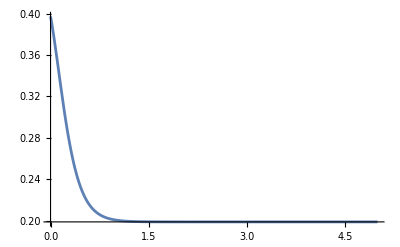

```mathematica
Areatorigin=1/(-1+Tanh[n T γ]^2)h (-4+4 π x Cot[π x]+4 Cos[π x] Sin[t+π x] Tanh[n T γ]-2 Csc[π x] (-2 π x+Sin[2 π x]) Sin[t+π x] Tanh[n T γ]+4 Tanh[n T γ]^2+ⅈ (Log[1+ⅈ ⅇ^(-ⅈ t) Tanh[n T γ]]-Log[1-ⅈ ⅇ^(ⅈ t) Tanh[n T γ]]-Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) Tanh[n T γ]]+Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) Tanh[n T γ]]) (2 Csc[π x] Sin[t+π x] Tanh[n T γ]+Cot[π x] (1+Tanh[n T γ]^2)));


bulkEE2ndorigin=-(π x)^(8h) (Gamma[3/2]Gamma[4h+1])/Gamma[4h+3/2](Cosh[2 n γ T]+Sinh[2 n γ T]Sin[t+π x])^(-4h);
Stotorigin=(  Areatorigin+ bulkEE2ndorigin)/.{t->-2 π a}//Simplify;
plot2=Plot[Stotorigin/.{T->1,γ->1.4,h->3, x->0.1, a->0.6},{n,0,5},PlotRange->All]
```

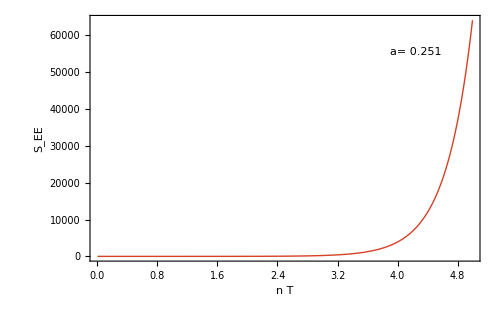

```mathematica
(*---Color definitions---*)col1=RGBColor[0.122,0.471,0.806];
col2=RGBColor[0.839,0.253,0.157];
col3=RGBColor[0.139,0.653,0.157];

(*---Compact parameter box---*)
paramBox=Framed[Column[{Row[{Graphics[{col1,Disk[]},ImageSize->10],Style[" a= 0.251",18]}]},Spacings->0.5],Background->White,FrameMargins->7,RoundingRadius->3,FrameStyle->Directive[Gray,AbsoluteThickness[0.8]]];

(*---Combined plot---*)
combinedPlot=Plot[{Re[Stotorigin/. {T->1,γ->1.4,h->3,x->0.01,a->0.251}]},{n,0,5},PlotRange->All,PlotStyle->{Directive[col2,Thick]},LabelStyle->Directive[Black,13],ImageSize->500,Epilog->Inset[paramBox,Scaled[{0.90,0.85}],Right],Frame->True,(*box around the plot area*)FrameLabel->{"n T","S_EE"},(*replaces AxesLabel*)FrameStyle->Directive[Black,AbsoluteThickness[1]],PlotRangePadding->{{0,0},{0,Scaled[0.05]}}]
```

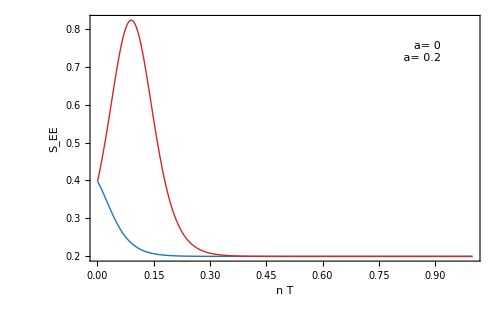

```mathematica
(*---Color definitions---*)col1=RGBColor[0.122,0.471,0.706];
col2=RGBColor[0.839,0.153,0.157];
col3=RGBColor[0.139,0.653,0.157];

(*---Compact parameter box---*)
paramBox=Framed[Column[{Row[{Graphics[{col1,Disk[]},ImageSize->10]," a= 0"}],Row[{Graphics[{col2,Disk[]},ImageSize->10]," a= 0.2"}]},Spacings->0.5],Background->White,FrameMargins->7,RoundingRadius->3,FrameStyle->Directive[Gray,AbsoluteThickness[0.8]]];

(*---Combined plot---*)
combinedPlot=Plot[{Re[Stotorigin/. {T->1,γ->7,h->3,x->0.1,a->0.0}],Re[Stotorigin/. {T->1,γ->7,h->3,x->0.1,a->0.2}]},{n,0,1},PlotRange->All,PlotStyle->{Directive[col1,Thick],Directive[col2,Thick]},LabelStyle->Directive[Black,13],ImageSize->500,Epilog->Inset[paramBox,Scaled[{0.90,0.85}],Right],Frame->True,(*box around the plot area*)FrameLabel->{"n T","S_EE"},(*replaces AxesLabel*)FrameStyle->Directive[Black,AbsoluteThickness[1]],PlotRangePadding->{{0,0},{0,Scaled[0.05]}}]
```

```mathematica
Export["/Users/semanti/Downloads/bulkheatingplot.pdf",combinedPlot,"PDF"]
```

/Users/semanti/Downloads/bulkheatingplot.pdf

```mathematica
Areatorigin=1/(-1+Tanh[n T γ]^2)h (-4+4 π x Cot[π x]+4 Cos[π x] Sin[t+π x] Tanh[n T γ]-2 Csc[π x] (-2 π x+Sin[2 π x]) Sin[t+π x] Tanh[n T γ]+4 Tanh[n T γ]^2+ⅈ (Log[1+ⅈ ⅇ^(-ⅈ t) Tanh[n T γ]]-Log[1-ⅈ ⅇ^(ⅈ t) Tanh[n T γ]]-Log[1+ⅈ ⅇ^(-ⅈ (t+2 π x)) Tanh[n T γ]]+Log[1-ⅈ ⅇ^(ⅈ (t+2 π x)) Tanh[n T γ]]) (2 Csc[π x] Sin[t+π x] Tanh[n T γ]+Cot[π x] (1+Tanh[n T γ]^2)));


bulkEE2ndorigin=-(π x)^(8h) (Gamma[3/2]Gamma[4h+1])/Gamma[4h+3/2](Cosh[2 n γ T]+Sinh[2 n γ T]Sin[t+ π x])^(-4h);
Stotorigin=(Areatorigin+  bulkEE2ndorigin)/.{t->-2 π a}//Simplify;
plot2=Plot3D[Stotorigin/.{T->1,γ->1.4,h->3, x->0.01}, {a,0.2,0.3},{n,0,5},PlotRange->All,AxesLabel->{Style["a",Bold,14],Style["nT",Bold,14],Style[Subscript[S,EE],Bold,14]},Background->White];
```

```mathematica
Show[plot2,ViewPoint->{1.3,-2.4,2.}]
```

-Graphics3D-